# Upscatter and decay of luminous dark matter in high resolution detectors

This notebook contains the analysis associated with arXiv:2208.08020

Gray (initialization) cells can/should be evaluated automatically
Red cells are computations (ones that usually take more than a few seconds)
Blue cells create plots
Orange cells read input files
Purple cells create output files

## Constants and functions

All units are in GeV unless otherwise explicitly noted

```mathematica
(*Constants*)
𝒸=2.997925 10^8;(*m/s*)
α=1/137.036;
ℏcGeVfm=0.19732698;(*GeV fm*)

(*Masses*)
mn=0.93956542052; (*neutron mass*)
amu=mn/1.00727; (*atomic mass unit*)
mp=0.93827; (*proton mass*)
me=0.000511; (*electron mass*)
```

Some useful units:

```mathematica
GeV=1;
MeV=10^-3(*GeV*);
keV=10^-6(*GeV*);
eV=10^-9(*GeV*);

Centimeter= 1/ℏcGeVfm 10^13(*GeV^-1*);
Kilometer= 10^5 Centimeter;
Second= 𝒸 10^2 Centimeter;
cm2s=(Centimeter^2/(1(*cm^2*)))(Second/(1(*s*)));
Kilogram=𝒸^2/(1.602 10^-19)(1(*GeV*))/10^9;
KilogramDay= (1 Kilogram)(24 3600 Second);
tonneYear=KilogramDay 1000 365.25;
```

DM astro parameters

```mathematica
ρχ=(0.3 (*GeV*))/Centimeter^3;
v0=238000/𝒸;
vlsr={0,v0,0};
ve=vlsr+{11.1,12.2,7.3}10^3/𝒸+{29.2,-0.1,5.9}10^3/𝒸//Norm;
vesc= 544000/𝒸;
VMAX=ve+vesc;
```

Earth’s crust abundances from Kouvaris and Emken (1802.04764, who got it from R. Rudnick and S. Gao, Composition of the continental crust, in Treatise on Geochemistry, pp. 1 – 64. Pergamon, Oxford, 2003):

```mathematica
NA=6.02 10^23/mol;
ρE=2.7g/Centimeter^3;
AN={16,28,27,56,40,39,23,24};
nN=ρE NA{(.466)/(16 g/mol),(.277)/(28 g/mol),(.081)/(27 g/mol),(.05)/(55.85 g/mol),(.036)/(40 g/mol),(.028)/(39.1 g/mol),(.026)/(23 g/mol),(.021)/(24.3 g/mol)};(*nuclei/volume*)
```

```mathematica
avgN=Plus@@nN ;
avgA=(Plus@@(AN*{.466,.277,.081,.05,.036,.028,.026,.021}))/(Plus@@{.466,.277,.081,.05,.036,.028,.026,.021});
```

Confidence levels:

```mathematica
CL1σ=InverseCDF[ChiSquareDistribution[2],.6827];
CL2σ=InverseCDF[ChiSquareDistribution[2],.9545];
CL90=InverseCDF[ChiSquareDistribution[2],.90];
```

Functions:

```mathematica
(*Reduced mass*)
μ[x_,y_]:=(x y)/(x+y)
(*Function to recalculate Vearth for different local standards of rest*)
Ve[V0_]={0,V0,0}+{11.1,12.2,7.3}10^3/𝒸+{29.2,-0.1,5.9}10^3/𝒸//Norm//Simplify[#,Assumptions->V0>0]&;
```

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

## Dark matter upscattering

### Kinematics

Inelastic kinematics

The final energy is: 1/2 μ v_i^2=E_1'+E_2'+δ
so   v_2'=μ/m_T^2(μ v_i^2-2δ)

```mathematica
ER==1/2 mT(μT/mT^2(μT Vi^2-2δ)+μT^2/mT^2 Vi^2-2 μT^2/mT^2 Vi^2 √( 1-(2δ)/(μT Vi^2))cosθCM)
```

ER==1/2 mT ((Vi^2 μT^2)/mT^2-(2 cosθCM Vi^2 √(1-(2 δ)/(Vi^2 μT)) μT^2)/mT^2+(μT (-2 δ+Vi^2 μT))/mT^2)

Simplifying by hand:

```mathematica
ER==μT^2/mT Vi^2(1-δ/(μT Vi^2)-√(1-(2δ)/(μT Vi^2))cosθCM)
```

ER==(Vi^2 (1-cosθCM √(1-(2 δ)/(Vi^2 μT))-δ/(Vi^2 μT)) μT^2)/mT

This agrees with Equation 91 of Ibe et al. (1707.07258)

Finding minimum dark matter velocity for a given recoil gives the familiar form:

```mathematica
Solve[{ER==μT^2/mT Vi^2(1-δ/(μT Vi^2)-√(1-(2δ)/(μT Vi^2))cosθCM)/.cosθCM->-1},Vi]
```

{{Vi→-(ER mT+δ μT)/(√2 √ER √mT μT)},{Vi→(ER mT+δ μT)/(√2 √ER √mT μT)}}

```mathematica
Vmin[ER_,δ_,mX_,mT_]=(ER mT+δ μ[mX,mT])/(√(2 mT ER) μ[mX,mT]);
```

Global max inelastic energy:

```mathematica
δmax[Vmax_,mX_,mT_]= (μ[mT,mX] Vmax^2)/2;
```

Maximum inelastic energy for a given nuclear recoil:

```mathematica
δmaxER[ER_,Vmax_,mX_,mT_]=√(2mT ER Vmax^2)-ER (mT+mX)/mX;
```

### Form factor

Helm form factor with s and r defined in fm:

```mathematica
Fhelm[q_,A_]=3(Sin[q r]-(q r)Cos[q r])/(q r)^3 Exp[(-(q s)^2)/2]/.{r->1/ℏcGeVfm((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9/ℏcGeVfm};
```

### Maxwell Boltzmann with cutoff

Define a Maxwell-Boltzmann speed distribution in Earth’s frame with a smooth cutoff to escape velocity:

```mathematica
fMB[v_,cosθ_,norm_]:=1/norm( Exp[-(v^2-2VE v cosθ+(VE)^2)/(V0)^2]-Exp[-VESC^2/V0^2])HeavisideTheta[(VESC)^2-(v^2-2VE v cosθ+(VE)^2)];
```

Find normalization:

```mathematica
Integrate[fMB[v ,csθ,1]2π v^2,{v,0,VE+VESC},{csθ,-1,1},Assumptions->{VE>0,VESC>0}]
```

ConditionalExpression[-(π (2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]))/VE, VE<VESC]

```mathematica
normfMB[VE_,VESC_]=-(π (2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]))/VE;
```

Find speed distribution by integrating over the angles, with work-around for the step function (which mathematica does not integrate properly):

```mathematica
Piecewise[{{1/normfMB[VE,VESC] Integrate[fMB[V,csθ,1]2π V^2,{csθ,-1,1},Assumptions->{V∈Reals,V>0,VE>0,VESC>0}],V<VESC-VE},{0,V≥VESC+VE}},1/normfMB[VE,VESC] Integrate[fMB[V,csθ,1]2π V^2,{csθ,1-((VESC)^2-(V-VE)^2)/(2VE V),1},Assumptions->{V∈Reals,V>0,VE>0,VESC>0}]]
```

Piecewise[{{(ⅇ^(-((V+VE)^2+VESC^2)/V0^2) V HeavisideTheta[(-(V-VE)^2+VESC^2)/(V VE)] (-ⅇ^((4 V VE+VESC^2)/V0^2) V0^2+ⅇ^((V+VE)^2/V0^2) (V0^2-(V-VE)^2+VESC^2)+(ⅇ^(VESC^2/V0^2) V0^2+ⅇ^((V+VE)^2/V0^2) (-V0^2+(V+VE)^2-VESC^2)) HeavisideTheta[(-(V+VE)^2+VESC^2)/(V VE)]))/(2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]), V<-VE+VESC}, {0, V≥VE+VESC}, {-(ⅇ^(-((V-VE)^2+VESC^2)/V0^2) V (ⅇ^(VESC^2/V0^2) V0^2+ⅇ^((V-VE)^2/V0^2) (-V0^2+(V-VE)^2-VESC^2)) HeavisideTheta[(-(V-VE)^2+VESC^2)/(V VE)])/(2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]), True}}]

Define distribution after integrating over angles:

```mathematica
Fv[V_?NumericQ,V0_,VESC_,VE_]=Piecewise[{{(ⅇ^(-((V+VE)^2+VESC^2)/V0^2) V HeavisideTheta[(-(V-VE)^2+VESC^2)/(V VE)] (-ⅇ^((4 V VE+VESC^2)/V0^2) V0^2+ⅇ^((V+VE)^2/V0^2) (V0^2-(V-VE)^2+VESC^2)+(ⅇ^(VESC^2/V0^2) V0^2+ⅇ^((V+VE)^2/V0^2) (-V0^2+(V+VE)^2-VESC^2)) HeavisideTheta[(-(V+VE)^2+VESC^2)/(V VE)]))/(2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]), V<-VE+VESC}, {0, V≥VE+VESC}, {-(ⅇ^(-((V-VE)^2+VESC^2)/V0^2) V (ⅇ^(VESC^2/V0^2) V0^2+ⅇ^((V-VE)^2/V0^2) (-V0^2+(V-VE)^2-VESC^2)) HeavisideTheta[(-(V-VE)^2+VESC^2)/(V VE)])/(2/3 ⅇ^(-VESC^2/V0^2) VE VESC (3 V0^2+2 VESC^2)-√π V0^3 VE Erf[VESC/V0]), True}}];
```

Full solution to integral ∫_(v>v_min) (f(v))/v ⅆv
from arXiv:1005.0579:

```mathematica
normMB[V0_,VESC_]=π^(3/2)(V0)^3(Erf[VESC/V0]-4/(√π)Exp[-(VESC/V0)^2](VESC/(2 V0)+1/3(VESC/V0)^3));
```

```mathematica
fOnvMB[vmin_?NumericQ,V0_?NumericQ,VESC_?NumericQ,VE_?NumericQ]=
Piecewise[
{
{(π^(3/2)(V0)^2)/(2 normMB[V0,VESC] VE/V0)(Erf[vmin/V0+VE/V0]-Erf[vmin/V0-VE/V0]-(4VE)/(√π V0)Exp[-(VESC/V0)^2](1+(VESC/V0)^2-VE^2/(3 V0^2)- (vmin/V0)^2)),
VE/V0+vmin/V0<VESC/V0},
{(π^(3/2)(V0)^2)/(2 normMB[V0,VESC] VE/V0)(Erf[VESC/V0]+Erf[-vmin/V0+VE/V0]-2/(√π)Exp[-(VESC/V0)^2]((VESC/V0)+VE/V0-(vmin/V0)-1/3(VE/V0 -2(VESC/V0) -(vmin/V0))((VESC/V0)+VE/V0-(vmin/V0))^2) ),vmin/V0>Abs[-VE/V0+VESC/V0] && (VE/V0+VESC/V0> vmin/V0)},
{Return[1/VE],VE/V0>vmin/V0+VESC/V0},
{Return[0],VE/V0+VESC/V0<vmin/V0}
}
];
```

Define function to use default values for halo parameters:

```mathematica
fOnvMB[vmin_?NumericQ]:=fOnvMB[vmin,v0,vesc,ve];
```

### Differential rate

```mathematica
dRdEr[Er_?NumericQ,δ_?NumericQ,σxp_?NumericQ,mx_?NumericQ,A_?NumericQ]:=
(ρχ/(2mx μ[mp,mx]^2))A^2 Fhelm[√(2(A amu) Er),A]^2 σxp fOnvMB[Vmin[Er,δ,mx,A amu]]
```

#### Sample nuclear recoil rates

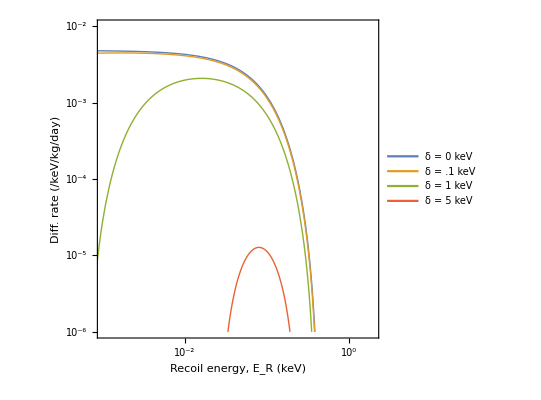

```mathematica
With[{MX=2GeV,σ=10^-45 Centimeter^2,A=131},
LogLogPlot[{
dRdEr[ER keV,        0,σ,MX,A]keV KilogramDay,
dRdEr[ER keV,.1keV,σ,MX,A]keV KilogramDay,
dRdEr[ER keV,1keV,σ,MX,A]keV KilogramDay,
dRdEr[ER keV,5 keV,σ,MX,A]keV KilogramDay},
{ER,10^-4,40},
PlotLegends->Legend[{"δ = 0 keV","δ = .1 keV","δ = 1 keV","δ = 5 keV"}],FrameLabel->{"Recoil energy, E_R (keV)","Diff. rate (/keV/kg/day)"},
PlotRange->{{10^-3,2},{10^-6,10^-2}},FrameTicks->{LogTicks[10^-6,1],LogTicks[10^-6,1]}]]
```

## Dark matter energy spectrum

### Halo DM spectrum

```mathematica
dNdExi[Exi_,mx_,V0_:v0,VESC_:vesc]=ρχ/mx Fv[√((2Exi)/mx),V0,VESC,Ve[V0]] √(mx/(2Exi));
```

### Earth scattered non-relativistic DM spectrum

#### Kinematics

Limits in terms of energy, in limit of δ << m_x:

```mathematica
Er==μT^2/mT(2Exi)/mx(1-(δ mx)/(μT 2Exi)+√(1-(2δ mx)/(μT 2 Exi)))/.{Er->Exi-Exf-δ,μT->μ[mx,mT]}//Solve[#,Exi]&//FullSimplify
```

{{Exi→(Exf (mT^2+mx^2)+mT (mT-mx) δ-2 √(Exf mT mx^2 (Exf mT+mT δ-mx δ)))/(mT-mx)^2},{Exi→(Exf (mT^2+mx^2)+mT (mT-mx) δ+2 √(Exf mT mx^2 (Exf mT+mT δ-mx δ)))/(mT-mx)^2}}

```mathematica
ExiMin[Exf_,mx_,δ_,mT_]:=(Exf (mT^2+mx^2)+mT (mT-mx) δ-2 √(Exf mT mx^2 (Exf mT+mT δ-mx δ)))/(mT-mx)^2
```

```mathematica
(Exf (mT^2+mx^2)+mT (mT-mx) δ-2 √(Exf mT mx^2 (Exf mT+mT δ-mx δ)))/(mT-mx)^2==(Exf (mT^2+mx^2)+mT (mT-mx) δ+2 √(Exf mT mx^2 (Exf mT+mT δ-mx δ)))/(mT-mx)^2//Solve[#,Exf]&//FullSimplify
```

{{Exf→0},{Exf→(-1+mx/mT) δ}}

```mathematica
ExfMin[mx_,δ_,mT_]=If[mx>mT,(mx/mT-1) δ,0];
```

```mathematica
TxiMaxGlobal[mx_,δ_,Vmax_]=1/2(mx+δ)(Vmax)^2 -δ;
```

```mathematica
Er==μT^2/mT v^2(1-δ/(μT v^2)+√(1-(2δ)/(μT v^2)))/.{Er->1/2 mx v^2-Exf-δ,μT->μ[mx,mT]}//Solve[#,v]&//FullSimplify[#,Assumptions->{Exf>0,mT>0}]&
```

{{v→-√((2 Exf (mT^2+mx^2)+2 mT (mT-mx) δ-4 mx √(Exf mT (Exf mT+(mT-mx) δ)))/((mT-mx)^2 mx))},{v→√((2 Exf (mT^2+mx^2)+2 mT (mT-mx) δ-4 mx √(Exf mT (Exf mT+(mT-mx) δ)))/((mT-mx)^2 mx))},{v→-√((2 Exf (mT^2+mx^2)+2 mT (mT-mx) δ+4 mx √(Exf mT (Exf mT+(mT-mx) δ)))/((mT-mx)^2 mx))},{v→√((2 Exf (mT^2+mx^2)+2 mT (mT-mx) δ+4 mx √(Exf mT (Exf mT+(mT-mx) δ)))/((mT-mx)^2 mx))}}

```mathematica
vMinF[Exf_,mx_,δ_,mT_]:=√((2 Exf (mT^2+mx^2)+2 mT (mT-mx) δ-4 mx √(Exf mT (Exf mT+(mT-mx) δ)))/((mT-mx)^2 mx))
```

The above is equivalent to Eq. 11 of 1312.1363:

```mathematica
vMin^2==(mT^2+mx^2)/(mT-mx)^2(2 Exf)/mx( 1+(mT (mT-mx) δ)/(Exf (mT^2+mx^2))-2 (mx mT)/(mT^2+mx^2) √(1+((mT-mx) δ)/(Exf mT)))
```

vMin^2==(2 Exf (mT^2+mx^2) (1+(mT (mT-mx) δ)/(Exf (mT^2+mx^2))-(2 mT mx √(1+((mT-mx) δ)/(Exf mT)))/(mT^2+mx^2)))/((mT-mx)^2 mx)

#### Differential scattering rate

Per target rate:

```mathematica
dRdEx[Ex_,δ_,σxp_,mx_,A_,V0_:v0,VESC_:vesc]:=If[Ex>ExfMin[mx,δ,A amu]&&ExiMin[Ex,mx,δ,A amu]<TxiMaxGlobal[mx,δ,VESC+Ve[V0]],(A amu)/(2 μ[mx,mp]^2)ρχ/mx A^2 σxp NIntegrate[Fhelm[√(2(A amu) (1/2 mx v^2-Ex-δ)),A]^2 Fv[v,V0,VESC,Ve[V0]] 1/v,{v,vMinF[Ex,mx,δ,A amu],VESC+Ve[V0]},PrecisionGoal->3],
0]
```

Remove the form factor to speed up (only valid for small momentum transfer):

```mathematica
dRdExApprox[Exf_,δ_,σxp_,mx_,A_,V0_:v0,VESC_:vesc]:=If[Exf>ExfMin[mx,δ,A amu],
(ρχ(A amu))/(2mx μ[mx,mp]^2)A^2 σxp fOnvMB[vMinF[Exf,mx,δ,A amu],V0,VESC,Ve[V0]],
0];
```

#### Compare incoming and outgoing spectra

```mathematica
norm2GeV=NIntegrate[dNdExi[Ex keV,2],{Ex,.01,20}];
norm5GeV=NIntegrate[dNdExi[Ex keV,5],{Ex,.01,20}];
norm15GeV=NIntegrate[dNdExi[Ex keV,15],{Ex,.01,50}];
```

```mathematica
rateTot2=ParallelTable[{Ex/keV,Sum[nN⟦ii⟧dRdEx[Ex,1keV,1,2GeV,AN⟦ii⟧],{ii,1,Length[AN]}]},{Ex,.01keV,5keV,.01keV}];
rateTot5=ParallelTable[{Ex/keV,Sum[nN⟦ii⟧dRdEx[Ex,1keV,1,5GeV,AN⟦ii⟧],{ii,1,Length[AN]}]},{Ex,.01keV,10keV,.01keV}];
rateTot15=ParallelTable[{Ex/keV,Sum[nN⟦ii⟧dRdEx[Ex,1keV,1,15GeV,AN⟦ii⟧],{ii,1,Length[AN]}]},{Ex,.01keV,25keV,.05keV}];
```

Normalize outgoing spectrum:

```mathematica
rateTot2[[All,2]]/=NIntegrate[Sum[nN⟦ii⟧dRdEx[Ex keV,1keV,1,2GeV,AN⟦ii⟧],{ii,1,Length[AN]}],{Ex,.01,5},PrecisionGoal->3];
rateTot5[[All,2]]/=NIntegrate[Sum[nN⟦ii⟧dRdEx[Ex keV,1keV,1,5GeV,AN⟦ii⟧],{ii,1,Length[AN]}],{Ex,.01,15},PrecisionGoal->3];
rateTot15[[All,2]]/=NIntegrate[Sum[nN⟦ii⟧dRdEx[Ex keV,1keV,1,15GeV,AN⟦ii⟧],{ii,1,Length[AN]}],{Ex,.01,45},PrecisionGoal->3];
```

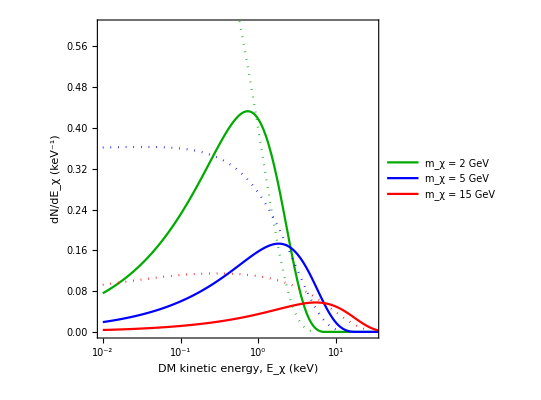

```mathematica
dmSpecPlot=Show[LogLinearPlot[{1/norm2GeV dNdExi[Ex keV,2],1/norm5GeV dNdExi[Ex keV,5],1/norm15GeV dNdExi[Ex keV,15]},{Ex,.01,50},
PlotPoints->100,PlotStyle->{Green//Darker,Blue,Red},
FrameTicks->{Automatic,LogTicks[10^-2,100]},
PlotRange->{{0,30},{0,.6}},
PlotLegends->Legend[{"m_χ = 2 GeV","m_χ = 5 GeV","m_χ = 15 GeV"},Position->{.8,.84},LegendFunction->framed],
FrameLabel->{"DM kinetic energy, E_χ (keV)","dN/dE_χ (keV^-1)"}],
ListLogLinearPlot[{rateTot2,rateTot5,rateTot15},Joined->True,PlotRange->All,
PlotStyle->{{Green//Darker,Dotted},{Blue,Dotted},{Red,Dotted}}]]
```

```mathematica
Export["figures/fig_DMspectrum.pdf",dmSpecPlot];
```

## LDM decay spectrum

### Define spectrum

#### Kinematics

Energy of the decay photon in rest frame of upscattered DM:

```mathematica
EγCoM[mx_,δ_]=((mx+δ)^2-mx^2)/(2(mx+δ));
```

Minimum kinetic energy of upscattered DM that can decay to a photon of energy E_γ in the lab frame:

```mathematica
TxMin[Eγ_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=(mx+δ)/2(Eγ/EγCoM[mx,δ]+EγCoM[mx,δ]/Eγ)-mx-δ//N
```

#### Differential spectrum

Spectrum of the decay photon, the absolute rate here is not reliable (it depends largely on the lifetime of the upscattered particle):

```mathematica
dNγdEG[Eg_,δ_,σxp_,mx_,V0_:v0,VESC_:vesc]:=
1/EγCoM[mx,δ] Sum[NIntegrate[nN⟦ii⟧dRdEx[Tx,δ,σxp,mx,AN⟦ii⟧,V0,VESC] (mx+δ)/(2 √((Tx+mx+δ)^2-(mx+δ)^2)),{Tx,TxMin[Eg,mx,δ],TxiMaxGlobal[mx,δ,VESC+Ve[V0]]},PrecisionGoal->3,AccuracyGoal->∞],{ii,Length[AN]}];
```

```mathematica
dNγdEgApprox[Eg_,δ_,σxp_,mx_,V0_:v0,VESC_:vesc]:=
1/EγCoM[mx,δ] Sum[NIntegrate[nN⟦ii⟧dRdExApprox[Tx,δ,σxp,mx,AN⟦ii⟧,V0,VESC] (mx+δ)/(2 √((Tx+mx+δ)^2-(mx+δ)^2)),{Tx,TxMin[Eg,mx,δ],TxiMaxGlobal[mx,δ,VESC+Ve[V0]]},PrecisionGoal->3,AccuracyGoal->∞],{ii,Length[AN]}];
```

### Example plots

#### Vary WIMP mass

```mathematica
With[{δ=5},
dataγA2=ParallelTable[{Egg/keV,dNγdEgApprox[Egg,δ keV,10^-41 Centimeter^2,2GeV]/dNγdEgApprox[δ keV,δ keV,10^-41 Centimeter^2,2GeV]},{Egg,(δ-8 10^-3)keV,(δ+8 10^-3)keV,(.1 10^-3)keV}];
dataγA5=ParallelTable[{Egg/keV,dNγdEgApprox[Egg,δ keV,10^-41 Centimeter^2,5GeV]/dNγdEgApprox[δ keV,δ keV,10^-41 Centimeter^2,5GeV]},{Egg,(δ-8 10^-3)keV,(δ+8 10^-3)keV,(.1 10^-3)keV}];
dataγA15=ParallelTable[{Egg/keV,dNγdEgApprox[Egg,δ keV,10^-41 Centimeter^2,15GeV]/dNγdEgApprox[δ keV,δ keV,10^-41 Centimeter^2,15GeV]},{Egg,(δ-8 10^-3)keV,(δ+8 10^-3)keV,(.1 10^-3)keV}];
];
```

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

«1 more identical outputs»

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

```mathematica
(*Epilog->Inset[Style["δ = 3 keV",18,FontFamily->"Times"],Scaled[{.1,.8}]]
```

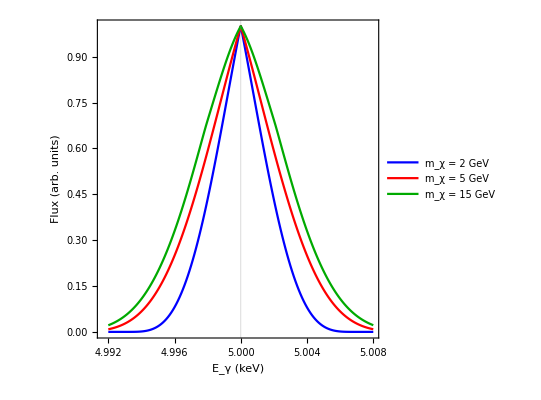

```mathematica
massSpectraPlot=ListPlot[{dataγA2,dataγA5,dataγA20},Joined->True,PlotRange->All,
PlotStyle->{Blue,Red,Green//Darker},
PlotLegends->Legend[{"m_χ = 2 GeV","m_χ = 5 GeV","m_χ = 15 GeV"},Position->{.8,.84},LegendFunction->framed,LegendMargins->3],
GridLines->{{5},None},
FrameLabel->{"E_γ (keV)","Flux (arb. units)"}]
```

```mathematica
Export["figures/fig_massDecaySpec.pdf",massSpectraPlot];
```

#### Vary velocity dist

```mathematica
With[{δDM=5keV,MX=5GeV},
(*standard velocity dist*)
dataγ2v=ParallelTable[{Egg/keV,dNγdEgApprox[Egg,δDM,1,MX]},{Egg,δDM-8 eV,δDM+8 eV,.2eV}];
dataγ2v[[All,2]]/=dNγdEgApprox[δDM,δDM,1,MX];

(*vary v0*)
dataγ1v=ParallelTable[{Egg/keV,dNγdEgApprox[Egg,δDM,1,MX,.5v0]},{Egg,δDM-8 eV,δDM+8 eV,.2eV}];
dataγ1v[[All,2]]/=dNγdEgApprox[δDM,δDM,1,MX,.5v0];

dataγ3v=ParallelTable[{Egg/keV,dNγdEgApprox[Egg,δDM,1,MX,1.5v0]},{Egg,δDM-8eV,δDM+8 eV,.2eV}];
dataγ3v[[All,2]]/=dNγdEgApprox[δDM,δDM,1,MX,1.5v0];

(*vary vesc*)
dataγ1vesc=ParallelTable[{Egg/keV,dNγdEgApprox[Egg,δDM,1,MX,v0,.5vesc]},{Egg,δDM-8 eV,δDM+8 eV,.2eV}];
dataγ1vesc[[All,2]]/=dNγdEgApprox[δDM,δDM,1,MX,v0,.5vesc];

dataγ3vesc=ParallelTable[{Egg/keV,dNγdEgApprox[Egg,δDM,1,MX,v0,1.5vesc]},{Egg,δDM-8 eV,δDM+8 eV,.2eV}];
dataγ3vesc[[All,2]]/=dNγdEgApprox[δDM,δDM,1,MX,v0,1.5vesc];
]
```

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

«6 more identical outputs»

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

«3 more identical outputs»

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

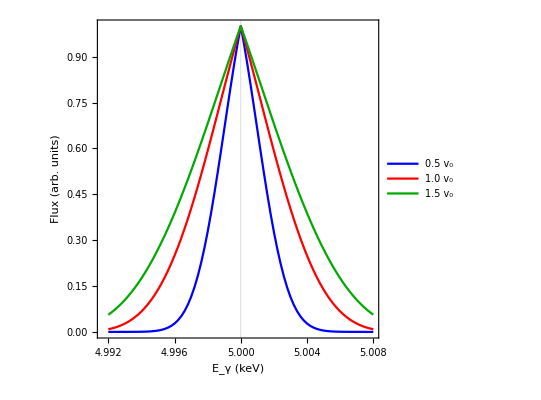
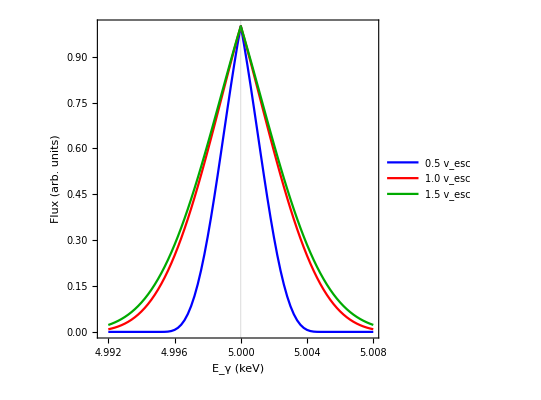

```mathematica
{v0specPlot,vescSpecPlot}=
{ListPlot[{dataγ1v,dataγ2v,dataγ3v},Joined->True,
PlotRange->All,PlotStyle->{Blue,Red,Green//Darker},
PlotLegends->Legend[{"0.5 v_0","1.0 v_0","1.5 v_0"},Position->{.82,.84},LegendFunction->framed],
GridLines->{{5},None},
FrameLabel->{"E_γ (keV)","Flux (arb. units)"}],
ListPlot[{dataγ1vesc,dataγ2v,dataγ3vesc},Joined->True,
PlotRange->All,PlotStyle->{Blue,Red,Green//Darker},
PlotLegends->Legend[{"0.5 v_esc","1.0 v_esc","1.5 v_esc"},Position->{.82,.84},LegendFunction->framed],
GridLines->{{5},None},
FrameLabel->{"E_γ (keV)","Flux (arb. units)"}]}
```

```mathematica
Export["figures/fig_v0DecaySpec.pdf",v0specPlot];
Export["figures/fig_vescDecaySpec.pdf",vescSpecPlot];
```

#### Combined plots

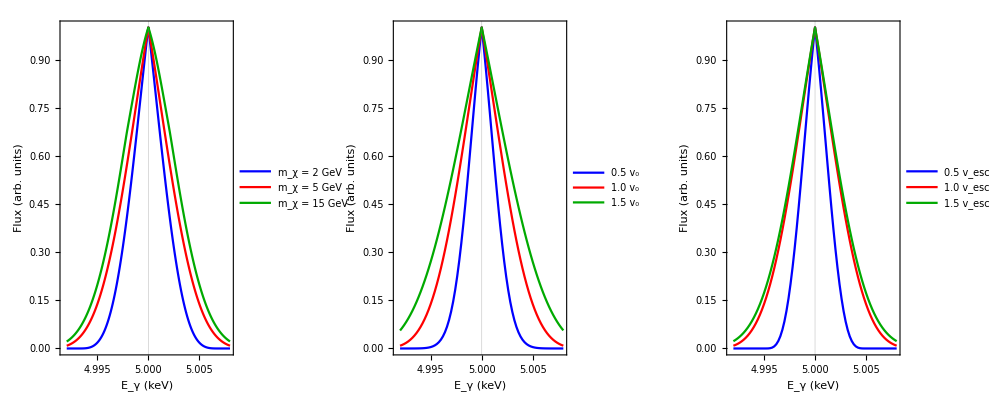

```mathematica
combSpecPlot=plotGrid[{{massSpectraPlot,v0specPlot,vescSpecPlot}},1000,420,ImagePadding->55]
```

```mathematica
Export["figures/fig_DecaySpectra.pdf",combSpecPlot];
```

### Define binned rate

```mathematica
binnedListNγEgApprox//Clear;
binnedListNγEgApprox[EgMin_,EgMax_,δ_,σxp_,mx_,nBins_:20,V0_:v0,VESC_:vesc]:=Module[{binWidth},
binWidth=(EgMax-EgMin)/nBins//N;
Return[Table[
{Eg+binWidth/2,1/EγCoM[mx,δ] NIntegrate[(avgN dRdExApprox[Tx,δ,σxp,mx,avgA,V0,VESC]) (mx+δ)/(2 √((Tx+mx+δ)^2-(mx+δ)^2)),{EG,Eg,Eg+binWidth},{Tx,Min[TxiMaxGlobal[mx,δ,VESC+Ve[V0]],TxMin[EG,mx,δ]],TxiMaxGlobal[mx,δ,VESC+Ve[V0]]},PrecisionGoal->2,AccuracyGoal->10]},
{Eg,EgMin,EgMax-binWidth,binWidth}]]]
```

## Discovery and inference prospects

### Parameters and functions

```mathematica
(*Detector parameters*)
REStoyStd=1eV;
REStoyHP=0.002eV;
BGtoyStd=0.25;(*SNR = 0.1*)
BGtoyHP=0.025; (*SNR = 1*)

(*Functions*)
toyBG[BGrate_,Nbins_]:=Table[BGrate,{Nbins}];
smearData[data_?ListQ,σE_?NumericQ,binW_?NumericQ]:=GaussianFilter[data,{(5 σE)/binW,σE/binW}]

sigPlusBG[μs_?NumericQ,δ_?NumericQ,mx_?NumericQ,BGrate_?NumericQ,Nbins_?IntegerQ,EMIN_?NumericQ,EMAX_?NumericQ,V0_:v0,VESC_:vesc]:=
Module[{sig,bg,norm},
sig=binnedListNγEgApprox[EMIN,EMAX,δ, 10^60,mx,Nbins,V0,VESC][[All,2]]; (*the large "cross section" reduces round off error*)
norm=Plus@@sig;
If[norm>0,sig*=μs/norm;];
bg= toyBG[BGrate,Nbins];
Return[sig+bg];
];

(*Define χ^2:*)
chiSq[dataObs_?ListQ,dataExp_?ListQ,exposure_?NumericQ]:=Plus@@(exposure((dataObs-dataExp)^2/dataExp));
```

### Benchmark 1: δ = 5 keV, m_χ=5GeV

```mathematica
(*Model parameters, σXP arbitrarily chosen to give 1 signal event*)
δToy=5keV;
MXtoy=5GeV;
σXPtoy=1.204 10^32 Centimeter^2;

(*ROI*)
EMINtoy=δToy-10 eV;
EMAXtoy=δToy+10 eV;
NBINStoy=100;
BINSWtoy=(EMAXtoy-EMINtoy)/NBINStoy;

(*calculate signal model*)
toySigData5keV5GeV=sigPlusBG[1,δToy,MXtoy,0,NBINStoy,EMINtoy,EMAXtoy,v0,vesc];
```

#### Significance

```mathematica
bgVsResPlot5keV=RegionPlot[{
chiSq[smearData[toySigData5keV5GeV+toyBG[10^NSR/NBINStoy,NBINStoy],σE eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],10^3]>9,
chiSq[smearData[toySigData5keV5GeV+toyBG[10^NSR/NBINStoy,NBINStoy],σE eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],100]>9,
chiSq[smearData[toySigData5keV5GeV+toyBG[10^NSR/NBINStoy,NBINStoy],σE eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],10]>9},
{σE,.001,10},{NSR,-1,3},PlotRange->{{0,10},{-1,3}},
PlotPoints->10,PlotStyle->{RGBColor[0.84,0.89,1.],RGBColor[0.52,0.64,1.],RGBColor[0.3,0.35,1.]},BoundaryStyle->None,
PlotLegends->Legend[{"N_γ = 10^3","N_γ = 10^2","N_γ = 10"},Type->"Swatch",LegendFunction->framed,Position->{.85,.85}],
FrameTicks->{{{{-1,10^1},{0,10^0},{1,Superscript[10,-1]},{2,Superscript[10,-2]},{3,Superscript[10,-3]}},Automatic},{Automatic,Automatic}},
FrameLabel->{"Resolution, σ_E (eV)","Background, SNR"}]
```

```mathematica
Export["figures/fig_bgVsRes_2p3keV.pdf",bgVsResPlot2p3keV
];
```

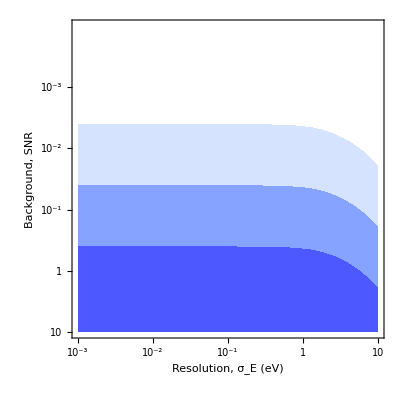

```mathematica
logbgVsResPlot5keV=RegionPlot[{
chiSq[smearData[toySigData5keV5GeV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],10^3]>9,
chiSq[smearData[toySigData5keV5GeV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],100]>9,
chiSq[smearData[toySigData5keV5GeV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],10]>9},
{σE,-3,1},{NSR,-1,4},PlotRange->{{-3,1},{-1,4}},
PlotPoints->10,PlotStyle->{RGBColor[0.84,0.89,1.],RGBColor[0.52,0.64,1.],RGBColor[0.3,0.35,1.]},BoundaryStyle->None,
FrameTicks->{{{{-1,10^1},{0,10^0},{1,Superscript[10,-1]},{2,Superscript[10,-2]},{3,Superscript[10,-3]}},Automatic},{{{-3,Superscript[10,-3]},{-2,Superscript[10,-2]},{-1,Superscript[10,-1]},{0,1},{1,10}},Automatic}},
FrameLabel->{"Resolution, σ_E (eV)","Background, SNR"}]
```

#### Mass confidence intervals

Standard detector assumptions:

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyStd,bgRate=BGtoyStd},
obsDat=smearData[toySigData5keV5GeV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
fitDatStd10mx  =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],  10]},{MX,logSpace[.1,40,60]}];
fitDatStd100mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],100]},{MX,logSpace[.1,40,60]}];
fitDatStd1000mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],1000] },{MX,logSpace[.1,40,60]}];
]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

High performance detector assumptions:

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigData5keV5GeV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
fitDatHP10mx   =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],  10]},{MX,logSpace[.1,40,60]}];
fitDatHP100mx =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],100]},{MX,logSpace[.1,40,60]}];
fitDatHP1000mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],1000]},{MX,logSpace[.1,40,60]}];
]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

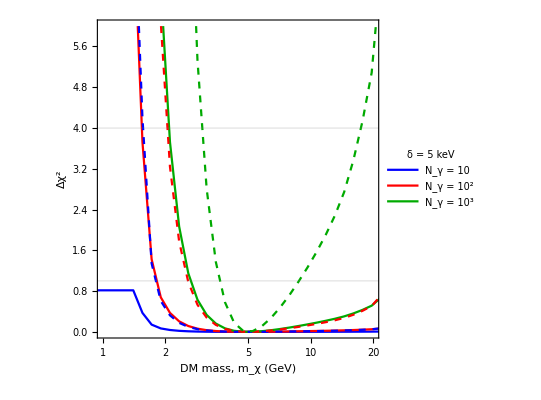

```mathematica
bestFitMassPlot=ListLogLinearPlot[{fitDatStd10mx,fitDatStd100mx,fitDatStd1000mx,fitDatHP10mx,fitDatHP100mx,fitDatHP1000mx},
FrameLabel->{"DM mass, m_χ (GeV)","Δχ^2"},Joined->True,GridLines->{None,{InverseCDF[ChiSquareDistribution[1],.6827],InverseCDF[ChiSquareDistribution[1],.9545]}},
PlotRange->{{1,20},{0,6}},FrameTicks->{Automatic,LogTicks[.01,10]},
PlotStyle->{Blue,Red,Green//Darker,{Blue,Dashed},{Red,Dashed},{Green//Darker,Dashed}},
PlotLegends->Legend[{"N_γ = 10","N_γ = 10^2","N_γ = 10^3"},Position->{.84,.82},LegendFunction->framed,LegendLabel->Style["δ = 5 keV",15,Black,FontFamily->"Times"]]]
(*Epilog->{Text[Style["σ_E = 0.1 eV\n    m_χ = 12 GeV",16.,FontFamily->"Times"],Scaled[{0.45,0.9}],{0,0}],Text[Style["",16.,FontFamily->"Times",FontColor->Red],Scaled[{0.2,0.95}],{0,0}]}*)
```

```mathematica
Export["figures/fig_bestFitMass_d5keV.pdf",bestFitMassPlot];
```

#### 2D Δχ^2

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigData5keV5GeV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
bestFit100MXvsVESC=ParallelTable[{MX,VESC 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,v0,VESC],σEres,BINSWtoy],100]},
{MX,.2,20,.1},{VESC,.5vesc,1.6vesc,.05vesc}];
bestFit1000MXvsVESC=ParallelTable[{MX,VESC 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,v0,VESC],σEres,BINSWtoy],1000]},
{MX,.2,20,.1},{VESC,.5vesc,1.6vesc,.05vesc}];]
```

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigData5keV5GeV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
bestFit100MXvsV0=ParallelTable[{MX,V0 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,vesc],σEres,BINSWtoy],100]},
{MX,.2,20,.1},{V0,.6v0,1.5v0,.05v0}];
bestFit1000MXvsV0=ParallelTable[{MX,V0 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,vesc ],σEres,BINSWtoy],1000]},
{MX,.2,20,.1},{V0,.6v0,1.5v0,.05v0}];]
```

Export computed χ^2:

```mathematica
Export["results/chiSq100_d5keV_m5GeV_mxVsVesc.dat",Flatten[bestFit100MXvsV0,1]];
Export["results/chiSq1000_d5keV_m5GeV_mxVsVesc.dat",Flatten[bestFit1000MXvsV0,1]];
Export["results/chiSq100_d5keV_m5GeV_mxVsV0.dat",Flatten[bestFit100MXvsV0,1]];
Export["results/chiSq1000_d5keV_m5GeV_mxVsV0.dat",Flatten[bestFit1000MXvsV0,1]];
```

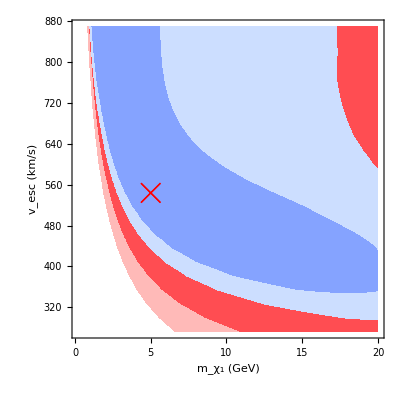

```mathematica
chiSq2DvescMXplot5keV5GeV=Show[ListContourPlot[Flatten[bestFit100MXvsVESC,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[1.,0.3,0.32],RGBColor[1.,0.73,0.72]
,None},
ContourStyle->None,
FrameLabel->{"m_χ_1 (GeV)","v_esc (km/s)"},FrameStyle->Directive[Black,Thickness[.004],18,FontFamily->"Times"]],ListContourPlot[Flatten[bestFit1000MXvsVESC,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[0.52,0.64,1.],RGBColor[0.8,0.87,1.],None},
ContourStyle->None],
ListPlot[{{5,vesc 𝒸/1000}},PlotMarkers->{"×",20},PlotStyle->{Red}]]
```

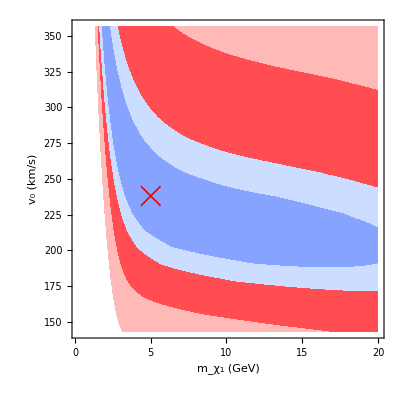

```mathematica
chiSq2Dv0MXplot5keV5GeV=Show[ListContourPlot[Flatten[bestFit100MXvsV0,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[1.,0.3,0.32],RGBColor[1.,0.73,0.72]
,None},
ContourStyle->None,
FrameLabel->{"m_χ_1 (GeV)","v_0 (km/s)"},FrameStyle->Directive[Black,Thickness[.004],18,FontFamily->"Times"]],ListContourPlot[Flatten[bestFit1000MXvsV0,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[0.52,0.64,1.],RGBColor[0.8,0.87,1.],None},
ContourStyle->None],
ListPlot[{{5,v0 𝒸/1000}},PlotMarkers->{"×",20},PlotStyle->{Red}]]
```

```mathematica
Export["figures/fig_2DchiSq_vescMx_5keV.pdf",chiSq2DvescMXplot2p3keV5GeV];
Export["figures/fig_2DchiSq_v0mx_5keV.pdf",chiSq2Dv0MXplot2p3keV5GeV];
```

### Benchmark 2: δ = 1 keV, m_χ=2GeV

```mathematica
(*Model parameters, σXP arbitrarily chosen, data get's normalized*)
δToy=1keV;
MXtoy=2GeV;
σXPtoy=10^32 Centimeter^2;

(*ROI parameters*)
EMINtoy=δToy-10 eV;
EMAXtoy=δToy+10 eV;
NBINStoy=100;
BINSWtoy=(EMAXtoy-EMINtoy)/NBINStoy;

(*calculate signal model*)
toySigData1keV=sigPlusBG[1,δToy,MXtoy,0,NBINStoy,EMINtoy,EMAXtoy,v0,vesc];
```

#### Significance

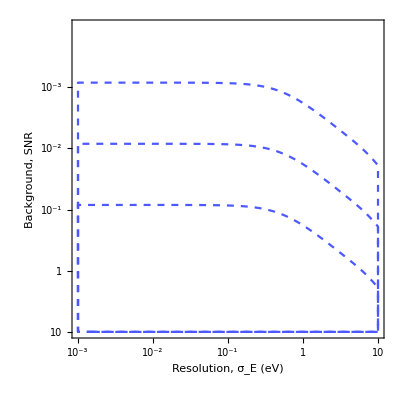

```mathematica
logbgVsResPlot1keV=RegionPlot[{
chiSq[smearData[toySigData1keV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],10^3]>9,
chiSq[smearData[toySigData1keV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],100]>9,
chiSq[smearData[toySigData1keV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],10]>9},
{σE,-3,1},{NSR,-1,4},PlotRange->{{-3,1},{-1,4}},
PlotPoints->20,PlotStyle->{Opacity[0,RGBColor[0.84,0.89,1.]],Opacity[0,RGBColor[0.52,0.64,1.]],Opacity[0,RGBColor[0.3,0.35,1.]]},BoundaryStyle->{{RGBColor[0.84,0.89,1.],Dashed},{Dashed,RGBColor[0.52,0.64,1.]},{RGBColor[0.3,0.35,1.],Dashed}},
FrameTicks->{{{{-1,10^1},{0,10^0},{1,Superscript[10,-1]},{2,Superscript[10,-2]},{3,Superscript[10,-3]}},Automatic},{{{-3,Superscript[10,-3]},{-2,Superscript[10,-2]},{-1,Superscript[10,-1]},{0,1},{1,10}},Automatic}},
FrameLabel->{"Resolution, σ_E (eV)","Background, SNR"}]
```

```mathematica
Export["figures/fig_bgVsRes.pdf",combSNRsigPlot];
```

#### Confidence intervals

Standard detector assumptions:

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyStd,bgRate=BGtoyStd},
obsDat=smearData[toySigData1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
fitDat1keVStd10mx  =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],  10]},{MX,logSpace[.1,100,60]}];
fitDat1keVStd100mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],100]},{MX,logSpace[.1,100,60]}];
fitDat1keVStd1000mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],1000] },{MX,logSpace[.1,100,60]}];
]
```

High performance detector assumptions:

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigData1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
fitDat1keVHP10mx   =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],  10]},{MX,logSpace[.1,100,60]}];
fitDat1keVHP100mx =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],100]},{MX,logSpace[.1,100,60]}];
fitDat1keVHP1000mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],1000]},{MX,logSpace[.1,100,60]}];
]
```

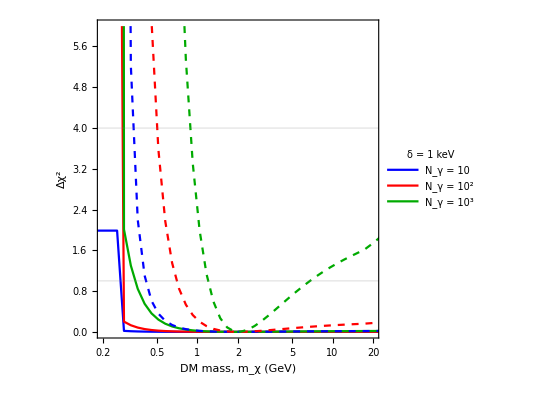

```mathematica
bestFitMassPlot1keV=ListLogLinearPlot[{fitDat1keVStd10mx,fitDat1keVStd100mx,fitDat1keVStd1000mx,fitDat1keVHP10mx,fitDat1keVHP100mx,fitDat1keVHP1000mx},
FrameLabel->{"DM mass, m_χ (GeV)","Δχ^2"},Joined->True,GridLines->{None,{InverseCDF[ChiSquareDistribution[1],.6827],InverseCDF[ChiSquareDistribution[1],.9545]}},
PlotRange->{{.2,20},{0,6}},PlotStyle->{Blue,Red,Green//Darker,{Blue,Dashed},{Red,Dashed},{Green//Darker,Dashed}},
PlotLegends->Legend[{"N_γ = 10","N_γ = 10^2","N_γ = 10^3"},Position->{.84,.82},LegendFunction->framed,LegendLabel->Style["δ = 1 keV",15,Black,FontFamily->"Times"]]]
```

```mathematica
Export["figures/fig_bestFitMass_d1keV.pdf",bestFitMassPlot1keV];
```

#### 2D Δχ^2

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigData1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
bestFit1keV100MXvsVESC=ParallelTable[{MX,VESC 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,v0,VESC],σEres,BINSWtoy],100]},
{MX,.1,20,.1},{VESC,.5vesc,1.6vesc,.05vesc}];
bestFit1keV1000MXvsVESC=ParallelTable[{MX,VESC 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,v0,VESC],σEres,BINSWtoy],1000]},
{MX,.1,20,.2},{VESC,.5vesc,1.6vesc,.05vesc}];]
```

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigData1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
bestFit1keV100MXvsV0=ParallelTable[{MX,V0 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,vesc],σEres,BINSWtoy],100]},
{MX,.1,20,.1},{V0,.6v0,1.5v0,.05v0}];
bestFit1keV1000MXvsV0=ParallelTable[{MX,V0 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,vesc],σEres,BINSWtoy],1000]},
{MX,.1,20,.1},{V0,.6v0,1.5v0,.05v0}];]
```

Export computed χ^2:

```mathematica
Export["results/chiSq100_d1keV_m1GeV_mxVsVesc.dat",Flatten[bestFit1keV100MXvsV0,1]];
Export["results/chiSq1000_d1keV_m1GeV_mxVsVesc.dat",Flatten[bestFit1keV1000MXvsV0,1]];
Export["results/chiSq100_d1keV_m1GeV_mxVsV0.dat",Flatten[bestFit1keV100MXvsV0,1]];
Export["results/chiSq1000_d1keV_m1GeV_mxVsV0.dat",Flatten[bestFit1keV1000MXvsV0,1]];
```

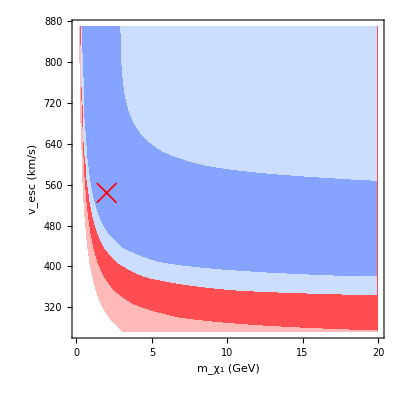

```mathematica
chiSq2DvescMXplot1keV2GeV=Show[ListContourPlot[Flatten[bestFit1keV100MXvsVESC,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[1.,0.3,0.32],RGBColor[1.,0.73,0.72]
,None},
ContourStyle->None,
FrameLabel->{"m_χ_1 (GeV)","v_esc (km/s)"},FrameStyle->Directive[Black,Thickness[.004],18,FontFamily->"Times"]],ListContourPlot[Flatten[bestFit1keV1000MXvsVESC,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[0.52,0.64,1.],RGBColor[0.8,0.87,1.],None},
ContourStyle->None],
ListPlot[{{2,vesc 𝒸/1000}},PlotMarkers->{"×",20},PlotStyle->{Red}]]
```

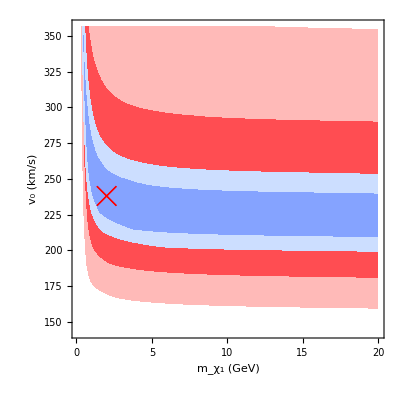

```mathematica
chiSq2Dv0MXplot1keV2GeV=Show[ListContourPlot[Flatten[bestFit1keV100MXvsV0,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[1.,0.3,0.32],RGBColor[1.,0.73,0.72]
,None},
ContourStyle->None,
FrameLabel->{"m_χ_1 (GeV)","v_0 (km/s)"},FrameStyle->Directive[Black,Thickness[.004],18,FontFamily->"Times"]],
ListContourPlot[Flatten[bestFit1keV1000MXvsV0,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[0.52,0.64,1.],RGBColor[0.8,0.87,1.],None},
ContourStyle->None],
ListPlot[{{2,v0 𝒸/1000}},PlotMarkers->{"×",20},PlotStyle->{Red}]]
```

```mathematica
Export["figures/fig_2DchiSq_vescMx_1keV.pdf",chiSq2DvescMXplot1keV2GeV];
Export["figures/fig_2DchiSq_v0mx_1keV.pdf",chiSq2Dv0MXplot1keV2GeV];
```

Marginalizing over mass

```mathematica
With[{μSignal=1,δDM=δToy,σEres=0.1REStoyHP,bgRate=.1},
obsDat=smearData[toySigData1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
bestFit100V0vsVESC=ParallelTable[{V0 𝒸/1000,VESC 𝒸/1000,
Mx=NArgMin[{chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX GeV,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,V0+ve-v0,VESC],σEres,BINSWtoy],100],1<MX<20},MX,PrecisionGoal->2,AccuracyGoal->2,Method->"NelderMead"];
chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,Mx,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,V0+ve-v0,VESC],σEres,BINSWtoy],100]},
{V0,.7v0,1.5v0,.1v0},{VESC,.7vesc,1.5vesc,.05vesc}];
bestFit1000V0vsVESC=ParallelTable[{V0 𝒸/1000,VESC 𝒸/1000,
Mx=NArgMin[{chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX GeV,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,V0+ve-v0,VESC],σEres,BINSWtoy],1000],1<MX<20},MX,PrecisionGoal->2,AccuracyGoal->2,Method->"NelderMead"];chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,Mx,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,V0+ve-v0,VESC],σEres,BINSWtoy],1000]},
{V0,.7v0,1.5v0,.1v0},{VESC,.7vesc,1.5vesc,.05vesc}];]
```

### Benchmark 3: δ = 0.1 keV, m_χ=0.1GeV

```mathematica
(*Model parameters, σXP arbitrarily chosen, data get's normalized*)
δToy=0.1keV;
MXtoy=0.1GeV;
σXPtoy=10^32 Centimeter^2;

(*ROI parameters*)
EMINtoy=δToy-10 eV;
EMAXtoy=δToy+10 eV;
NBINStoy=100;
BINSWtoy=(EMAXtoy-EMINtoy)/NBINStoy;

(*calculate signal model*)
toySigDatap1keV=sigPlusBG[1,δToy,MXtoy,0,NBINStoy,EMINtoy,EMAXtoy,v0,vesc];
```

#### Significance

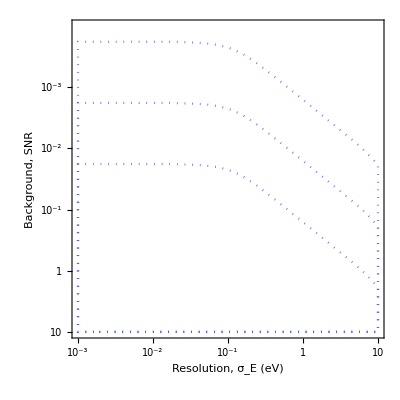

```mathematica
logbgVsResPlotp1keV=RegionPlot[{
chiSq[smearData[toySigDatap1keV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],10^3]>9,
chiSq[smearData[toySigDatap1keV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],100]>9,
chiSq[smearData[toySigDatap1keV+toyBG[10^NSR/NBINStoy,NBINStoy],(10^σE) eV,BINSWtoy],toyBG[10^NSR/NBINStoy,NBINStoy],10]>9},
{σE,-3,1},{NSR,-1,4},PlotRange->{{-3,1},{-1,4}},
PlotPoints->20,PlotStyle->{Opacity[0,RGBColor[0.84,0.89,1.]],Opacity[0,RGBColor[0.52,0.64,1.]],Opacity[0,RGBColor[0.3,0.35,1.]]},BoundaryStyle->{{RGBColor[0.84,0.89,1.],Dotted},{Dotted,RGBColor[0.52,0.64,1.]},{RGBColor[0.3,0.35,1.],Dotted}},
FrameTicks->{{{{-1,10^1},{0,10^0},{1,Superscript[10,-1]},{2,Superscript[10,-2]},{3,Superscript[10,-3]}},Automatic},{{{-3,Superscript[10,-3]},{-2,Superscript[10,-2]},{-1,Superscript[10,-1]},{0,1},{1,10}},Automatic}},
FrameLabel->{"Resolution, σ_E (eV)","Background, SNR"}]
```

#### Confidence intervals

```mathematica
(*Model parameters, σXP arbitrarily chosen, data get's normalized*)
δToy=0.1keV;
MXtoy=0.1GeV;
σXPtoy=10^32 Centimeter^2;

(*ROI parameters*)
EMINtoy=δToy-1 eV;
EMAXtoy=δToy+1 eV;
NBINStoy=100;
BINSWtoy=(EMAXtoy-EMINtoy)/NBINStoy;

(*calculate signal model*)
toySigDatap1keV=sigPlusBG[1,δToy,MXtoy,0,NBINStoy,EMINtoy,EMAXtoy,v0,vesc];
```

Standard detector assumptions:

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyStd,bgRate=BGtoyStd},
obsDat=smearData[toySigDatap1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
fitDatp1keVStd10mx  =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],  10]},{MX,logSpace[.01,10,60]}];
fitDatp1keVStd100mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],100]},{MX,logSpace[.01,10,60]}];
fitDatp1keVStd1000mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],1000] },{MX,logSpace[.01,10,60]}];
]
```

High performance detector assumptions:

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigDatap1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
fitDatp1keVHP10mx   =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],  10]},{MX,logSpace[.02,10,60]}];
fitDatp1keVHP100mx =ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],100]},{MX,logSpace[.02,10,60]}];
fitDatp1keVHP1000mx=ParallelTable[{MX,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy],σEres,BINSWtoy],1000]},{MX,logSpace[.02,10,60]}];
]
```

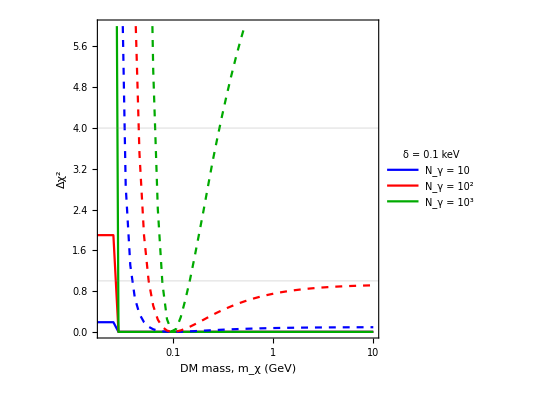

```mathematica
bestFitMassPlotp1keV=ListLogLinearPlot[{fitDatp1keVStd10mx,fitDatp1keVStd100mx,fitDatp1keVStd1000mx,fitDatp1keVHP10mx,fitDatp1keVHP100mx,fitDatp1keVHP1000mx},
FrameLabel->{"DM mass, m_χ (GeV)","Δχ^2"},Joined->True,GridLines->{None,{InverseCDF[ChiSquareDistribution[1],.6827],InverseCDF[ChiSquareDistribution[1],.9545]}},
PlotRange->{{.02,10},{0,6}},FrameTicks->{Automatic,LogTicks[10^-2,10]},
PlotStyle->{Blue,Red,Green//Darker,{Blue,Dashed},{Red,Dashed},{Green//Darker,Dashed}},
PlotLegends->Legend[{"N_γ = 10","N_γ = 10^2","N_γ = 10^3"},Position->{.84,.82},LegendFunction->framed,LegendLabel->Style["δ = 0.1 keV",15,Black,FontFamily->"Times"]]]
```

```mathematica
Export["figures/fig_bestFitMass_d1keV.pdf",bestFitMassPlot1keV];
```

#### 2D Δχ^2

```mathematica
(*Model parameters, σXP arbitrarily chosen, data get's normalized*)
δToy=0.1keV;
MXtoy=0.1GeV;
σXPtoy=10^32 Centimeter^2;

(*ROI parameters*)
EMINtoy=δToy-1 eV;
EMAXtoy=δToy+1 eV;
NBINStoy=100;
BINSWtoy=(EMAXtoy-EMINtoy)/NBINStoy;

(*calculate signal model*)
toySigDatap1keV=sigPlusBG[1,δToy,MXtoy,0,NBINStoy,EMINtoy,EMAXtoy,v0,vesc];
```

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigDatap1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
bestFitp1keV100MXvsVESC=ParallelTable[{MX,VESC 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,v0,VESC],σEres,BINSWtoy],100]},
{MX,.03,10,.03},{VESC,.5vesc,1.6vesc,.05vesc}];
bestFitp1keV1000MXvsVESC=ParallelTable[{MX,VESC 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,v0,VESC],σEres,BINSWtoy],1000]},
{MX,.03,10,.03},{VESC,.5vesc,1.6vesc,.05vesc}];]
```

```mathematica
With[{μSignal=1,δDM=δToy,σEres=REStoyHP,bgRate=BGtoyHP},
obsDat=smearData[toySigDatap1keV+toyBG[bgRate,NBINStoy],σEres,BINSWtoy];
bestFitp1keV100MXvsV0=ParallelTable[{MX,V0 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,vesc],σEres,BINSWtoy],100]},
{MX,.03,5,.02},{V0,.6v0,1.5v0,.05v0}];
bestFitp1keV1000MXvsV0=ParallelTable[{MX,V0 𝒸/1000,chiSq[ obsDat,smearData[ sigPlusBG[1,δDM,MX,bgRate,NBINStoy,EMINtoy,EMAXtoy,V0,vesc],σEres,BINSWtoy],1000]},
{MX,.03,5,.02},{V0,.6v0,1.5v0,.05v0}];]
```

Export computed χ^2:

```mathematica
Export["results/chiSq100_d0p1keV_m100MeV_mxVsVesc.dat",Flatten[bestFitp1keV100MXvsVESC,1]];
Export["results/chiSq1000_d0p1keV_m100MeV_mxVsVesc.dat",Flatten[bestFitp1keV1000MXvsVESC,1]];
Export["results/chiSq100_d0p1keV_m100MeV_mxVsV0.dat",Flatten[bestFitp1keV100MXvsVESC,1]];
Export["results/chiSq1000_d0p1keV_m100MeV_mxVsV0.dat",Flatten[bestFitp1keV1000MXvsVESC,1]];
```

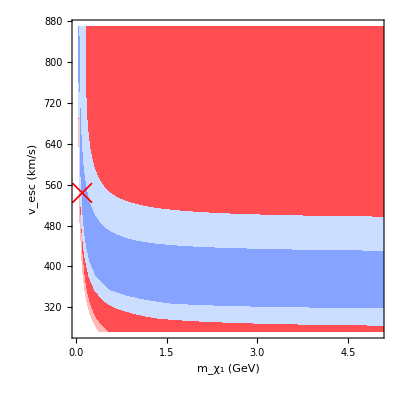

```mathematica
chiSq2DvescMXplotp1keV=Show[ListContourPlot[Flatten[bestFitp1keV100MXvsVESC,1],PlotRange->{{.03,5},All},
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[1.,0.3,0.32],RGBColor[1.,0.73,0.72]
,None},
ContourStyle->None,
FrameLabel->{"m_χ_1 (GeV)","v_esc (km/s)"},FrameStyle->Directive[Black,Thickness[.004],18,FontFamily->"Times"]],ListContourPlot[Flatten[bestFitp1keV1000MXvsVESC,1],PlotRange->All,
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[0.52,0.64,1.],RGBColor[0.8,0.87,1.],None},
ContourStyle->None],
ListPlot[{{.1,vesc 𝒸/1000}},PlotMarkers->{"×",20},PlotStyle->{Red}]]
```

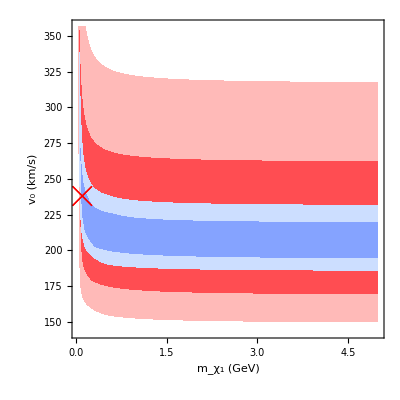

```mathematica
chiSq2Dv0MXplotp1keV=Show[ListContourPlot[Flatten[bestFitp1keV100MXvsV0,1],
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[1.,0.3,0.32],RGBColor[1.,0.73,0.72]
,None},PlotRange->{{.03,5},All},
ContourStyle->None,
FrameLabel->{"m_χ_1 (GeV)","v_0 (km/s)"},FrameStyle->Directive[Black,Thickness[.004],18,FontFamily->"Times"]],
ListContourPlot[Flatten[bestFitp1keV1000MXvsV0,1],PlotRange->{{.03,10},All},
Contours->{CL1σ,CL2σ},ContourShading->{RGBColor[0.52,0.64,1.],RGBColor[0.8,0.87,1.],None},
ContourStyle->None],
ListPlot[{{.1,v0 𝒸/1000}},PlotMarkers->{"×",20},PlotStyle->{Red}]]
```

```mathematica
Export["figures/fig_2DchiSq_vescMx_1keV.pdf",chiSq2DvescMXplot1keV2GeV];
Export["figures/fig_2DchiSq_v0mx_1keV.pdf",chiSq2Dv0MXplot1keV2GeV];
```

### Combined plots

```mathematica
combSNRsigPlot=Show[logbgVsResPlot5keV,logbgVsResPlot1keV,logbgVsResPlotp1keV,RegionPlot[{1>2,1>2,1>2},
{σE,.001,10},{NSR,-1,3},
PlotStyle->{RGBColor[0.84,0.89,1.],RGBColor[0.52,0.64,1.],RGBColor[0.3,0.35,1.]},BoundaryStyle->None,
PlotLegends->Legend[{"N_γ = 10^3","N_γ = 10^2","N_γ = 10"},Type->"Swatch",LegendFunction->framed,Position->{.85,.85}],
FrameTicks->{{{{-1,10^1},{0,10^0},{1,Superscript[10,-1]},{2,Superscript[10,-2]},{3,Superscript[10,-3]}},Automatic},{Automatic,Automatic}},
FrameLabel->{"Resolution, σ_E (eV)","Background, SNR"}],ListPlot[{{Log10[.002],0},{Log10[1],1}},PlotMarkers->Style["×",18],PlotStyle->Red]]
```

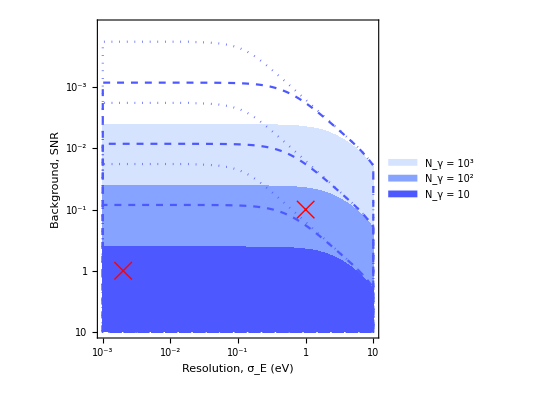

```mathematica
Export["figures/fig_bgVsRes.pdf",combSNRsigPlot];
```

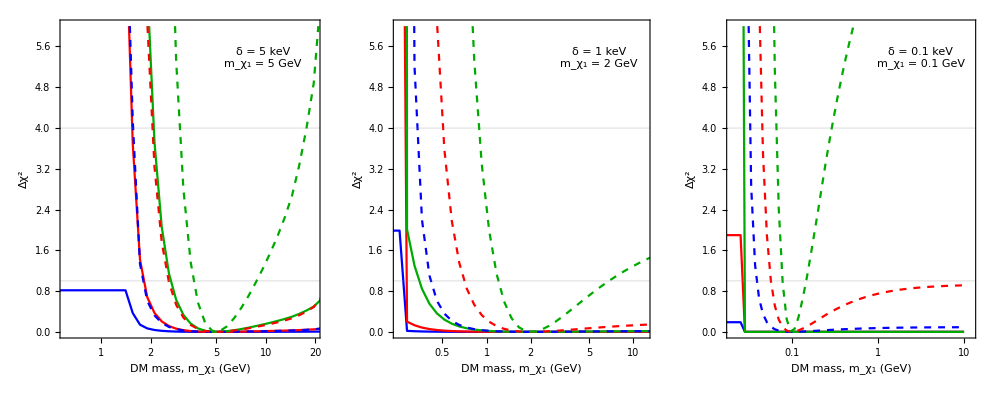

```mathematica
bestFitMassPlot5keV=ListLogLinearPlot[{fitDatStd10mx,fitDatStd100mx,fitDatStd1000mx,fitDatHP10mx,fitDatHP100mx,fitDatHP1000mx},
FrameLabel->{"DM mass, m_χ_1 (GeV)","Δχ^2"},Joined->True,GridLines->{None,{InverseCDF[ChiSquareDistribution[1],.6827],InverseCDF[ChiSquareDistribution[1],.9545]}},
PlotRange->{{.6,20},{0,6}},FrameTicks->{Automatic,LogTicks[.01,10]},
PlotStyle->{Blue,Red,Green//Darker,{Blue,Dashed},{Red,Dashed},{Green//Darker,Dashed}},
Epilog->Inset[Style["    δ = 5 keV\nm_χ_1 = 5 GeV",16.,FontFamily->"Times"]//framed,Scaled[{0.78,0.88}]]];
bestFitMassPlot1keV=ListLogLinearPlot[{fitDat1keVStd10mx,fitDat1keVStd100mx,fitDat1keVStd1000mx,fitDat1keVHP10mx,fitDat1keVHP100mx,fitDat1keVHP1000mx},
FrameLabel->{"DM mass, m_χ_1 (GeV)","Δχ^2"},Joined->True,GridLines->{None,{InverseCDF[ChiSquareDistribution[1],.6827],InverseCDF[ChiSquareDistribution[1],.9545]}},
PlotRange->{{.25,12},{0,6}},FrameTicks->{Automatic,LogTicks[10^-2,10]},
PlotStyle->{Blue,Red,Green//Darker,{Blue,Dashed},{Red,Dashed},{Green//Darker,Dashed}},
Epilog->{Inset[Style["    δ = 1 keV\nm_χ_1 = 2 GeV",16.,FontFamily->"Times"]//framed,Scaled[{0.8,0.88}]]}];
bestFitMassPlotp1keV=ListLogLinearPlot[{fitDatp1keVStd10mx,fitDatp1keVStd100mx,fitDatp1keVStd1000mx,fitDatp1keVHP10mx,fitDatp1keVHP100mx,fitDatp1keVHP1000mx},
FrameLabel->{"DM mass, m_χ_1 (GeV)","Δχ^2"},Joined->True,GridLines->{None,{InverseCDF[ChiSquareDistribution[1],.6827],InverseCDF[ChiSquareDistribution[1],.9545]}},
PlotRange->{{.02,12},{0,6}},FrameTicks->{Automatic,LogTicks[10^-2,10]},
PlotStyle->{Blue,Red,Green//Darker,{Blue,Dashed},{Red,Dashed},{Green//Darker,Dashed}},
Epilog->{Inset[Style["    δ = 0.1 keV\nm_χ_1 = 0.1 GeV",16.,FontFamily->"Times"]//framed,Scaled[{0.78,0.88
}]]}];

combSpecPlotMX=plotGrid[{{bestFitMassPlot5keV,bestFitMassPlot1keV,bestFitMassPlotp1keV}},1000,400,ImagePadding->54]
```

```mathematica
Export["figures/fig_comb_mxFit.pdf",combSpecPlotMX];
```

Tweak the padding:

```mathematica
Options[plotGridMod]={ImagePadding->40};
plotGridMod[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w-40},{0,h-50}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
newMxTicks=Join[Table[{mx,mx,.014},{mx,0,15,5}],Table[{mx,None,.005},{mx,0,20,1}]];
```

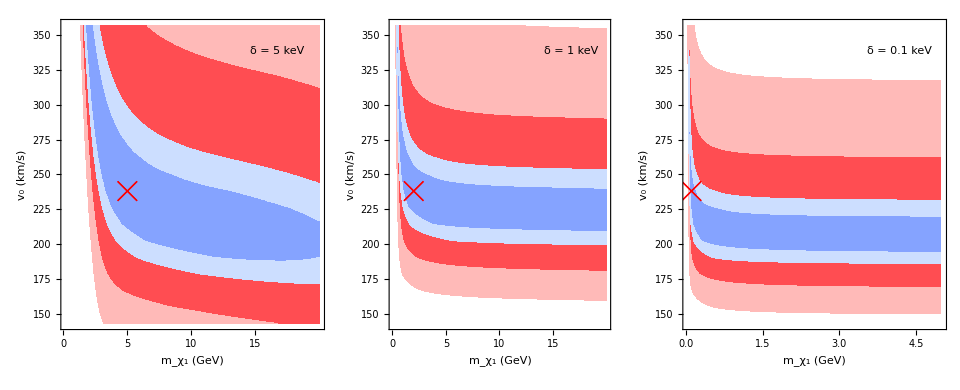

```mathematica
combPlotV0=plotGridMod[{{Show[chiSq2Dv0MXplot5keV5GeV/.(FrameTicks->_)->(FrameTicks->{{Automatic,Automatic},{newMxTicks,newMxTicks}}),Epilog->Inset[Style["δ = 5 keV",16,FontFamily->"Times"]//framed,Scaled[{.82,.9}]]],Show[chiSq2Dv0MXplot1keV2GeV/.(FrameTicks->_)->(FrameTicks->{{Automatic,Automatic},{newMxTicks,newMxTicks}}),Epilog->Inset[Style["δ = 1 keV",16,FontFamily->"Times"]//framed,Scaled[{.82,.9}]]],Show[chiSq2Dv0MXplotp1keV,Epilog->Inset[Style["δ = 0.1 keV",16,FontFamily->"Times"]//framed,Scaled[{.82,.9}]]]}},960,390,ImagePadding->54]
```

```mathematica
Export["figures/fig_comb_mxV0fit.pdf",combPlotV0];
```

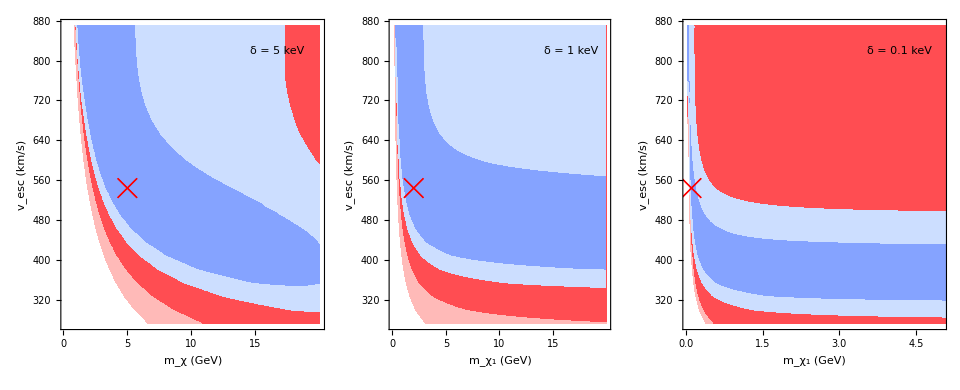

```mathematica
combPlotVESC=plotGridMod[{{Show[chiSq2DvescMXplot2p3keV5GeV/.(FrameTicks->_)->(FrameTicks->{{Automatic,Automatic},{newMxTicks,newMxTicks}}),Epilog->Inset[Style["δ = 5 keV",16,FontFamily->"Times"]//framed,Scaled[{.82,.9}]]],Show[chiSq2DvescMXplot1keV2GeV/.(FrameTicks->_)->(FrameTicks->{{Automatic,Automatic},{newMxTicks,newMxTicks}}),Epilog->Inset[Style["δ = 1 keV",16,FontFamily->"Times"]//framed,Scaled[{.82,.9}]]],Show[chiSq2DvescMXplotp1keV,Epilog->Inset[Style["δ = 0.1 keV",16,FontFamily->"Times"]//framed,Scaled[{.82,.9}]]]}},960,390,ImagePadding->54]
```

```mathematica
Export["figures/fig_comb_mxVescFit.pdf",combPlotVESC];
```

## Distinguishing models

### Electron exothermic scattering

As an example of another model that fits a sharply peaked signal we will use Bramante’s “Electric but not eclectic” model of inelastic scattering on electrons

#### Import and define atomic scattering function for xenon

Import atomic scattering factors computed with DarkARC:

```mathematica
NotebookDirectory[]//SetDirectory;
xe5s=Import["data/Xe_5s.dat"];
xe5p=Import["data/Xe_5p.dat"];

xe4s=Import["data/Xe_4s.dat"];
xe4p=Import["data/Xe_4p.dat"];
xe4d=Import["data/Xe_4d.dat"];

xe3s=Import["data/Xe_3s.dat"];
xe3p=Import["data/Xe_3p.dat"];
xe3d=Import["data/Xe_3d.dat"];

QMIN=1keV;
QMAX=1MeV;
KMIN=.1keV;
KMAX=100keV;
qPoints=logSpace[QMIN,QMAX,Length[xe4d]];
kPoints=logSpace[KMIN,KMAX,Length[xe4d[[1]]]];
```

Format for use:

```mathematica
xe3sDat=Table[{{qPoints⟦ii⟧,kPoints⟦jj⟧},xe3s⟦jj,ii⟧},{ii,1,Length[xe3s]},{jj,1,Length[xe3s[[1]]]}];
xe3pDat=Table[{{qPoints⟦ii⟧,kPoints⟦jj⟧},xe3p⟦jj,ii⟧},{ii,1,Length[xe3p]},{jj,1,Length[xe3p[[1]]]}];
xe3dDat=Table[{{qPoints⟦ii⟧,kPoints⟦jj⟧},xe3d⟦jj,ii⟧},{ii,1,Length[xe3d]},{jj,1,Length[xe3d[[1]]]}];

xe4sDat=Table[{{qPoints⟦ii⟧,kPoints⟦jj⟧},xe4s⟦jj,ii⟧},{ii,1,Length[xe4s]},{jj,1,Length[xe4s[[1]]]}];
xe4pDat=Table[{{qPoints⟦ii⟧,kPoints⟦jj⟧},xe4p⟦jj,ii⟧},{ii,1,Length[xe4p]},{jj,1,Length[xe4p[[1]]]}];
xe4dDat=Table[{{qPoints⟦ii⟧,kPoints⟦jj⟧},xe4d⟦jj,ii⟧},{ii,1,Length[xe4d]},{jj,1,Length[xe4d[[1]]]}];

xe5sDat=Table[{{qPoints⟦ii⟧,kPoints⟦jj⟧},xe5s⟦jj,ii⟧},{ii,1,Length[xe5s]},{jj,1,Length[xe5s[[1]]]}];
xe5pDat=Table[{{qPoints⟦ii⟧,kPoints⟦jj⟧},xe5p⟦jj,ii⟧},{ii,1,Length[xe5p]},{jj,1,Length[xe5p[[1]]]}];
```

Create interpolation objects:

```mathematica
xe3sFF=xe3sDat//Flatten[#,1]&//Interpolation[#,InterpolationOrder->1]&;
xe3pFF=xe3pDat//Flatten[#,1]&//Interpolation[#,InterpolationOrder->1]&;
xe3dFF=xe3dDat//Flatten[#,1]&//Interpolation[#,InterpolationOrder->1]&;

xe4sFF=xe4sDat//Flatten[#,1]&//Interpolation[#,InterpolationOrder->1]&;
xe4pFF=xe4pDat//Flatten[#,1]&//Interpolation[#,InterpolationOrder->1]&;
xe4dFF=xe4dDat//Flatten[#,1]&//Interpolation[#,InterpolationOrder->1]&;

xe5sFF=xe5sDat//Flatten[#,1]&//Interpolation[#,InterpolationOrder->1]&;
xe5pFF=xe5pDat//Flatten[#,1]&//Interpolation[#,InterpolationOrder->1]&;
```

Check functions work as expected:

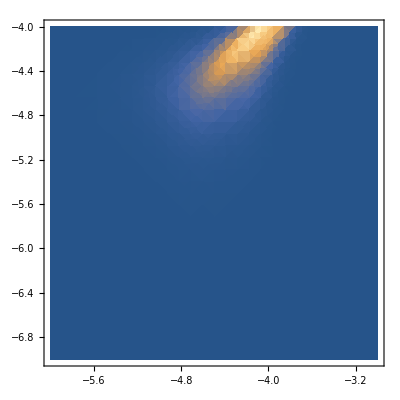

```mathematica
DensityPlot[xe3dFF[10^q,10^kk],{q,Log10[QMIN],QMAX//Log10},{kk,KMIN//Log10,KMAX//Log10},PlotRange->All]
```

To reproduce Bramante, use the curve they took from Roberts:

```mathematica
NotebookDirectory[]//SetDirectory;
KeXE=Import["data/xe_atomic_K.csv"]//Interpolation[#,InterpolationOrder->1]&;
```

Define the two atomic ionization form factors:

```mathematica
Ke[Er_?NumericQ,q_?NumericQ]:=If[q<1.05keV||q>1.6MeV,0,KeXE[q/keV]];
KeFull[Er_?NumericQ,q_?NumericQ]:=If[q>QMAX || q<QMIN || Er>KMAX || Er<KMIN,0,xe3sFF[q,Er]UnitStep[Er-orbitsEnDat[[5]]]+xe3pFF[q,Er]UnitStep[Er-orbitsEnDat[[6]]]+xe3dFF[q,Er]UnitStep[Er-orbitsEnDat[[7]]]+xe4sFF[q,Er]UnitStep[Er-orbitsEnDat[[10]]]+xe4pFF[q,Er]UnitStep[Er-orbitsEnDat[[11]]]+xe4dFF[q,Er]UnitStep[Er-orbitsEnDat[[15]]]+xe5sFF[q,Er]UnitStep[Er-orbitsEnDat[[5]]]+xe5pFF[q,Er]]UnitStep[Er-orbitsEnDat[[16]]];
```

#### New form factors

Provided by Ashlee and Ben

```mathematica
KeStepDat=Import["data/AshAndBen/afbe_table-Xe_V.txt","Table"]//Drop[#,2]&;
KeStepDat [[All,1]]*=MeV;(*convert units*)
orbitsEnDat=-1eV(Import["data/AshAndBen/enHF-Xe.txt","Table"]//Drop[#,1]&)[[All,4]];
intF=(Interpolation[#,InterpolationOrder->1]&/@Table[KeStepDat[[All,{1,ii}]],{ii,2,Length[KeStepDat[[1]]]-1}]);
KeStepFull[Ee_,q_]=Plus@@(((#@q&)/@intF)*Table[UnitStep[Ee-orbitsEnDat[[ii]]],{ii,1,Length[orbitsEnDat]}]);
```

#### Kinematics

Bounds on the velocity:

```mathematica
vmin[k_?NumericQ,Er_?NumericQ,mx_?NumericQ,δDM_?NumericQ]:=Abs[(Er+δDM)/k+k/(2mx)]
(*Global min for all k*)
vmin[Er_?NumericQ,mx_?NumericQ,δDM_?NumericQ]:=√Max[2/mx(Er+δDM),0]
```

Bounds on the momentum:

```mathematica
qMin[Er_?NumericQ,mx_?NumericQ,δDM_?NumericQ]:=Abs[mx VMAX-√((mx VMAX)^2-2 mx (δDM+Er))]
qMax[Er_?NumericQ,mx_?NumericQ,δDM_?NumericQ]:=Abs[mx VMAX+√((mx VMAX)^2-2 mx (δDM+Er))]
```

#### Differential rates

Define rates for reproducing Bramante and also a full calculation of my own:

```mathematica
dRdEr[Er_?NumericQ,δDM_?NumericQ,σe_?NumericQ,mx_?NumericQ]:=
(1/(131.3amu))(ρχ/mx)(1/(2me))(1/(me α))^2 σe NIntegrate[fOnvMB[vmin[q,Er,mx,δDM],(240 10^3)/𝒸,(600 10^3)/𝒸,Ve[(240 10^3)/𝒸]] q Ke[Er,q],
{q,qMin[Er,mx,δDM],Min[QMAX,qMax[Er,mx,δDM]]},PrecisionGoal->4]
```

```mathematica
dRdErKfull[Er_?NumericQ,δDM_?NumericQ,σe_?NumericQ,mx_?NumericQ]:=
(1/(131.3amu))(ρχ/mx)(1/(2me))(1/(me α))^2 σe NIntegrate[fOnvMB[vmin[q,Er,mx,δDM],v0,vesc,Ve[v0]] q KeFull[Er,q],
{q,qMin[Er,mx,δDM],Min[QMAX,qMax[Er,mx,δDM]]},PrecisionGoal->3]
```

```mathematica
dRdErKfullStep[Er_?NumericQ,δDM_?NumericQ,σe_?NumericQ,mx_?NumericQ]:=
(1/(131.3amu))(ρχ/mx)(1/(2me))(1/(me α))^2 σe NIntegrate[fOnvMB[vmin[q,Er,mx,δDM],v0,vesc,Ve[v0]] q KeStepFull[Er,q],
{q,qMin[Er,mx,δDM],Min[QMAX,qMax[Er,mx,δDM]]},PrecisionGoal->3]
```

```mathematica
datRepro=ParallelTable[{er/keV,tonneYear keV dRdEr[er,-2.8keV,5.3/2 10^-45 Centimeter^2,.1GeV]},{er,logSpace[1keV,3.2keV,200]}];
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

```mathematica
datFull=ParallelTable[{er/keV,tonneYear keV dRdErKfull[er,-2.8keV, 5.3/2 10^-45 Centimeter^2,.1GeV]},{er,logSpace[2keV,3.2keV,200]}];
```

```mathematica
datHF=ParallelTable[{er/keV,tonneYear keV dRdErKfullStep[er,-2.8keV, 5.3/2 10^-45 Centimeter^2,.1GeV]},{er,logSpace[2keV,3.2keV,200]}];
```

Import Bramante’s rate for comparison:

```mathematica
datBramante=Import["data/xe1tExcess_inelasticE_m100MeV.csv"];
```

Plot a comparison of the rates:

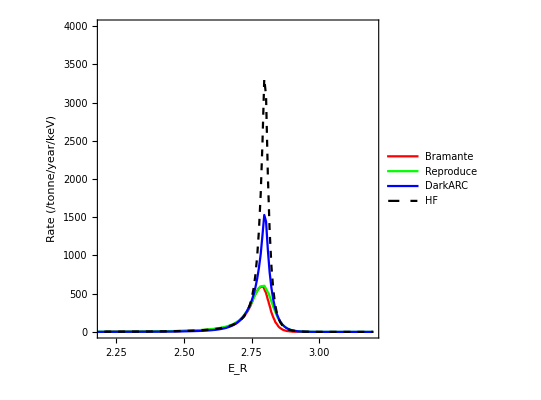

```mathematica
ListPlot[{datBramante,datRepro,datFull,datHF},Joined->True,ImageSize->400,
PlotLegends->Legend[{"Bramante","Reproduce","DarkARC","HF"},Position->{.2,.8}],
PlotStyle->{Red,Green,Blue,{Black,Dashed}},
PlotRange->{{2.2,3.2},{0,4000}},
FrameLabel->{"E_R","Rate (/tonne/year/keV)"}]
```

#### Smeared rates

Define a gaussian smeared electron scattering rate with energy resolution of 0.5keV to represent current technology:

```mathematica
f[EE_,er_]=PDF[NormalDistribution[er,0.5keV],EE];
dRdErSmeared[Er_?NumericQ,δDM_?NumericQ,σe_?NumericQ,mx_?NumericQ]:=
(1/(131.3amu))(ρχ/mx)(1/(2me))(1/(me α))^2 σe NIntegrate[fOnvMB[vmin[q,ER,mx,δDM],v0,vesc,Ve[v0]] q KeFull[ER,q]f[ER,Er],{ER,Max[Er-4 0.5keV,.1keV],Er+4 0.5keV},
{q,Max[qMin[ER,mx,δDM],QMIN],Min[qMax[ER,mx,δDM],QMAX]},PrecisionGoal->3]
exoErateSmeared[ErMin_?NumericQ,ErMax_?NumericQ,δDM_?NumericQ,σe_?NumericQ,mx_?NumericQ]:=
(1/(131.3amu))(ρχ/mx)(1/(2me))(1/(me α))^2 σe NIntegrate[fOnvMB[vmin[q,ER,mx,δDM],v0,vesc,Ve[v0]] q KeFull[ER,q]f[ER,Er],{Er,ErMin,ErMax},{ER,Max[Er-4σResXe1t[Er/keV]keV,.1keV],Er+4σResXe1t[Er/keV]keV},
{q,Max[qMin[ER,mx,δDM],QMIN],Min[qMax[ER,mx,δDM],QMAX]},PrecisionGoal->3]
```

### Compare exothermic electron scattering and LDM

Define a smeared LDM signal:

```mathematica
dataγA5=ParallelTable[{Egg,dNγdEgApprox[Egg keV,5 keV,10^-41 Centimeter^2,5GeV]/dNγdEgApprox[5 keV,5 keV,10^-41 Centimeter^2,5GeV]},{Egg,4.95,5.05,.001}]
δ5LDM=dataγA5//Interpolation[#,InterpolationOrder->1]&;
δ5LDMnorm=NIntegrate[δ5LDM[x],{x,4.99,5.01}];
LDMδsig[Eγ_,rate_]:=rate/δ5LDMnorm δ5LDM[Eγ]UnitStep[Eγ-4.95]UnitStep[5.05-Eγ];
smearedLine[ER_,σReskeV_,rate_]:=NIntegrate[LDMδsig[er,rate](ⅇ^(-(er-ER)^2/(2 (σReskeV)^2)))/((σReskeV) √(2 π)),{er,Max[ER-4 σReskeV,.1],ER+4 σReskeV}];
bg[er_]=1;
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{4.95,0.},{4.951,0.},{4.952,0.},{4.953,0.},{4.954,0.},{4.955,0.},{4.956,0.},{4.957,0.},{4.958,0.},{4.959,0.},{4.96,0.},{4.961,0.},{4.962,0.},{4.963,0.},{4.964,0.},{4.965,0.},{4.966,0.},{4.967,0.},{4.968,0.},{4.969,0.},{4.97,0.},{4.971,0.},{4.972,0.},{4.973,0.},{4.974,0.},{4.975,0.},{4.976,0.},{4.977,0.},{4.978,0.},{4.979,0.},{4.98,0.},{4.981,0.},{4.982,0.},{4.983,0.},{4.984,0.},{4.985,0.},{4.986,0.},{4.987,0.},{4.988,0.},{4.989,1.49422×10^-7},{4.99,0.000146258},{4.991,0.00176386},{4.992,0.00852988},{4.993,0.027084},{4.994,0.0668083},{4.995,0.138179},{4.996,0.249564},{4.997,0.403209},{4.998,0.592034},{4.999,0.799089},{5.,1.},{5.001,0.798088},{5.002,0.591188},{5.003,0.402655},{5.004,0.249325},{5.005,0.138179},{5.006,0.0669267},{5.007,0.0272156},{5.008,0.00861821},{5.009,0.00180155},{5.01,0.000153786},{5.011,2.07355×10^-7},{5.012,0.},{5.013,0.},{5.014,0.},{5.015,0.},{5.016,0.},{5.017,0.},{5.018,0.},{5.019,0.},{5.02,0.},{5.021,0.},{5.022,0.},{5.023,0.},{5.024,0.},{5.025,0.},{5.026,0.},{5.027,0.},{5.028,0.},{5.029,0.},{5.03,0.},{5.031,0.},{5.032,0.},{5.033,0.},{5.034,0.},{5.035,0.},{5.036,0.},{5.037,0.},{5.038,0.},{5.039,0.},{5.04,0.},{5.041,0.},{5.042,0.},{5.043,0.},{5.044,0.},{5.045,0.},{5.046,0.},{5.047,0.},{5.048,0.},{5.049,0.},{5.05,0.}}

Calculate binned event data, unsmeared:

```mathematica
bgDat=ParallelTable[{er,bg[er]},{er,logSpace[2,6,200]}];
datLine=ParallelTable[{er,LDMδsig[er,1]+bg[er]},{er,logSpace[4.9,5.1,1000]}];
normExo=NIntegrate[dRdErKfull[er,-5keV, 10^-45 Centimeter^2,.1GeV],{er,4keV,6keV},PrecisionGoal->3];
datExoE=ParallelTable[{er/keV,keV/normExo dRdErKfull[er,-5keV,  10^-45 Centimeter^2,.1GeV]+bg[er]},{er,logSpace[4.5keV,5.2keV,100]}];
```

and smeared:

```mathematica
datLineSmeared=ParallelTable[{er,smearedLine[er,.5,1]+bg[er]},{er,logSpace[4,6,200]}];
datExoEsmeared=ParallelTable[{er/keV, keV/normExo dRdErSmeared[er,-5keV, 10^-45 Centimeter^2,.1GeV]+bg[er]},{er,logSpace[4keV,6keV,80]}];
```

Plot comparison of the spectra:

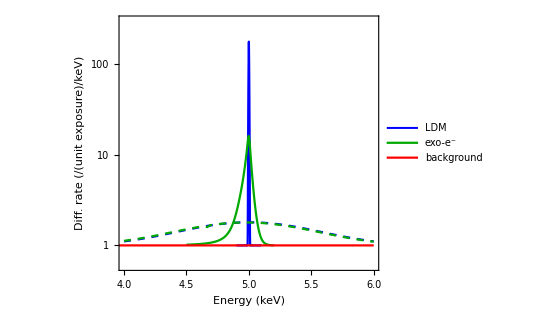

```mathematica
compareSigPlot=Show[ListLogPlot[{datLine,datExoE,bgDat},Joined->True,AspectRatio->.8,
FrameLabel->{"Energy (keV)","Diff. rate (/(unit exposure)/keV)"},PlotStyle->{{Thickness[.004],Blue},Green//Darker,Red},PlotLegends->Legend[{"LDM","exo-e^-","background"},Position->{.80,.8},LegendFunction->framed],
PlotRange->{{4,6},{.6,300}},FrameTicks->{LogTicks[1,10^3],Automatic}],
ListLogPlot[{datLineSmeared,datExoEsmeared},Joined->True,AspectRatio->.8,
PlotStyle->{{Blue,Dashed},{Dashed,Green//Darker}}]]
```

```mathematica
Export["figures/fig_comp_data.pdf",compareSigPlot];
```

### Define binned rates

```mathematica
(*Detector parameters*)
EMIN=4;
EMAX=6;
NBINS=40;
BINSW=(EMAX-EMIN)/NBINS;
σRES=0.5;
(*Model parameters*)
δDM=5keV;
```

Define function for binned background rate:

```mathematica
binnedBG[bg_, nBins_]:=Table[bg/nBins,{nBins}];
```

Tabulate unsmeared rate for exothermic case:

```mathematica
datExoRate=ParallelTable[{er/keV,dRdErKfull[er,-δDM,10^-45 Centimeter^2,.1GeV]},{er,EMIN keV,EMAX keV,.01keV}];
exoRate=Interpolation[datExoRate,InterpolationOrder->1];
normExoRate=NIntegrate[exoRate[er],{er,EMIN,EMAX}];
```

Define binned rate function:

```mathematica
binnedListExo[Ne_,σE_]:=Table[
{EL+BINSW/2,Ne NIntegrate[exoRate[er]/normExoRate(ⅇ^(-(er-ER)^2/(2 (σE)^2)))/((σE) √(2 π)),{ER,EL,EL+BINSW},{er,Max[ER-4σE,0],ER+4σE},PrecisionGoal->2,AccuracyGoal->10]},
{EL,EMIN,EMAX-BINSW,BINSW}]
```

```mathematica
sigPlusBGexo[Ns_?NumericQ,σE_?NumericQ,bgSNR_?NumericQ]:=Module[{sig},
sig=binnedListExo[Ns,σE][[All,2]];
Return[sig+binnedBG[Ns/bgSNR,NBINS]];
];
```

Define line signal:

```mathematica
binnedSmearedLDM[Ns_,σE_]:=Table[
{EL+BINSW/2,NIntegrate[LDMδsig[eγ,Ns](ⅇ^(-(eγ-ER)^2/(2 (σE)^2)))/((σE) √(2 π)),{ER,EL,EL+BINSW},{eγ,Max[ER-4σE,0],ER+4σE},PrecisionGoal->3]},
{EL,EMIN,EMAX-BINSW,BINSW}]
```

```mathematica
sigPlusBGldm[Ns_?NumericQ,σE_?NumericQ,bgSNR_?NumericQ]:=Module[{sig},
sig=binnedSmearedLDM[Ns,σE][[All,2]];
Return[sig+binnedBG[Ns/bgSNR,NBINS]];
];
```

### Statistical functions

Log likelihood for a Poisson distribution

```mathematica
logL[exp_,obs_]:=Plus@@(-exp+obs Log[exp]-Log[obs!]);
```

Define log-likelihood ratio test statistic:

```mathematica
qμ[Nexp_,Nobs_]:=-2(logL[Nexp,Nobs]-logL[Nexp,Nexp])
```

### Calculation and plot

```mathematica
With[{bgSNR=.1,σRes=σRES},
exoObs=ParallelTable[sigPlusBGexo[ 1,RES,bgSNR],{RES,σRes{1,1/2,1/5,1/50}}];
LDMexp=ParallelTable[sigPlusBGldm[ 1,RES,bgSNR],{RES,σRes{1,1/2,1/5,1/50}}];
datRes=ParallelTable[{Ne,√qμ[Ne LDMexp[[i]],Ne exoObs[[i]]]},
{i,1,Length[exoObs]},{Ne,logSpace[10,10000,25]}];
];
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«2 more identical outputs»

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integra
tion is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

```mathematica
With[{bgSNR=1,σRes=σRES},
exoObsHP=ParallelTable[sigPlusBGexo[ 1,RES,bgSNR],{RES,σRes{1,1/2,1/5,1/50}}];
LDMexpHP=ParallelTable[sigPlusBGldm[ 1,RES,bgSNR],{RES,σRes{1,1/2,1/5,1/50}}];
datResHP=ParallelTable[{Ne,√qμ[Ne LDMexpHP[[i]],Ne exoObsHP[[i]]]},
{i,1,Length[exoObs]},{Ne,logSpace[10,10000,25]}];
];
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«2 more identical outputs»

```mathematica
sigPlot=Show[ListLogLinearPlot[datRes,Joined->True,
PlotStyle->{Blue,Red,Green//Darker,Orange},PlotRange->{{10,10000},{1,5}},
FrameLabel->{"Number of signal events","Significance , Z (σ)"},AspectRatio->.7,FrameTicks->{Automatic,LogTicks[1,10^4]},
PlotLegends->(Legend[{"0.5 keV","0.25 keV","0.1 keV","10 eV"},Position->{.53,1},LegendFunction->framed,LegendLayout->"Row",LegendMarkerSize->10])],
ListLogLinearPlot[datResHP,Joined->True,
PlotStyle->{{Dashed,Blue},{Dashed,Red},{Dashed,Green//Darker},{Dashed,Orange}}
]]
```

```mathematica
Export["figures/fig_comp_sig.pdf",sigPlot];
```

## Appendix

#### Comparison of atomic form factors

Compare the form factors (Roberts is only at E=2keV):

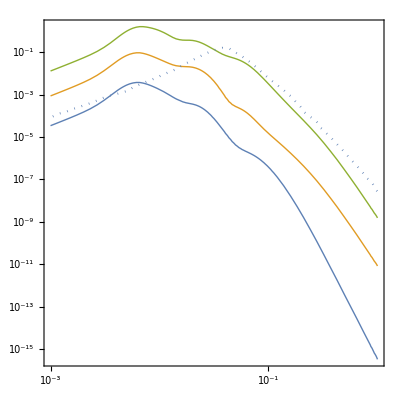

```mathematica
Show[LogLogPlot[{KeFull[.1keV,q MeV],KeFull[.5keV,q MeV],KeFull[2keV,q MeV]},{q,.001,1}],
LogLogPlot[Ke[2keV,q MeV],{q,.001,1},PlotStyle->Dotted]]
```

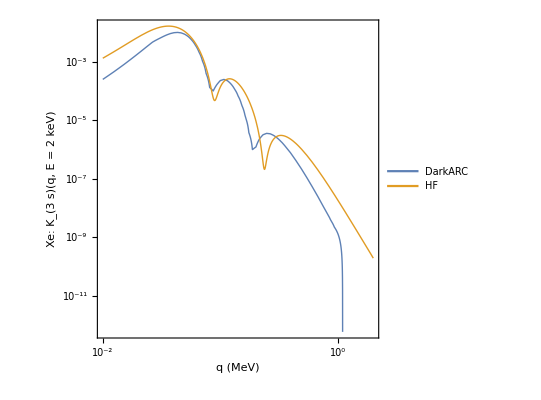
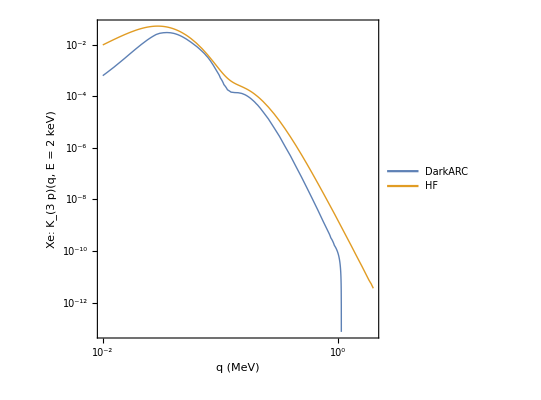
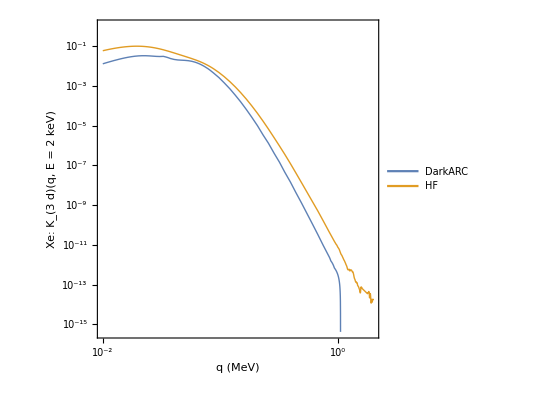

```mathematica
{LogLogPlot[{xe3sFF[q MeV,2keV],intF[[5]][q MeV]},{q,.01,2},
FrameLabel->{"q (MeV)","Xe: K_(3  s)(q, E = 2 keV)"},PlotLegends->Legend[{"DarkARC","HF"}]],
LogLogPlot[{xe3pFF[q MeV,2keV],intF[[6]][q MeV]+intF[[7]][q MeV]},{q,.01,2},
FrameLabel->{"q (MeV)","Xe: K_(3  p)(q, E = 2 keV)"},PlotLegends->Legend[{"DarkARC","HF"}]],
LogLogPlot[{xe3dFF[q MeV,2keV],intF[[8]][q MeV]+intF[[9]][q MeV]},{q,.01,2},
FrameLabel->{"q (MeV)","Xe: K_(3  d)(q, E = 2 keV)"},PlotLegends->Legend[{"DarkARC","HF"}]]}
```

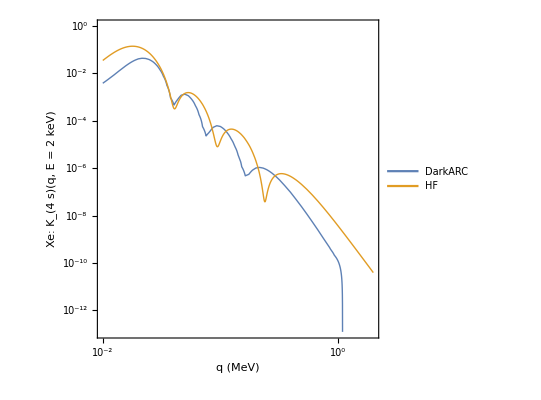
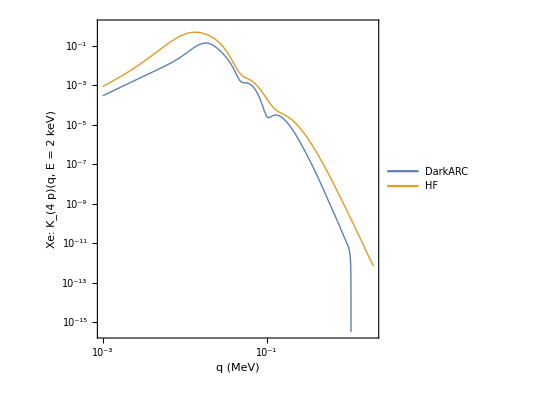
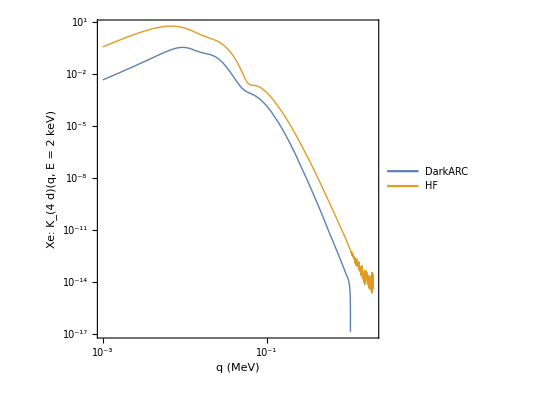

```mathematica
{LogLogPlot[{xe4sFF[q MeV,2keV],intF[[10]][q MeV]},{q,.01,2},
FrameLabel->{"q (MeV)","Xe: K_(4  s)(q, E = 2 keV)"},PlotLegends->Legend[{"DarkARC","HF"}]],
LogLogPlot[{xe4pFF[q MeV,2keV],intF[[11]][q MeV]+intF[[12]][q MeV]},{q,.001,2},
FrameLabel->{"q (MeV)","Xe: K_(4  p)(q, E = 2 keV)"},PlotLegends->Legend[{"DarkARC","HF"}]],
LogLogPlot[{xe4dFF[q MeV,2keV],intF[[13]][q MeV]+intF[[14]][q MeV]},{q,.001,2},
FrameLabel->{"q (MeV)","Xe: K_(4  d)(q, E = 2 keV)"},PlotLegends->Legend[{"DarkARC","HF"}]]}
```

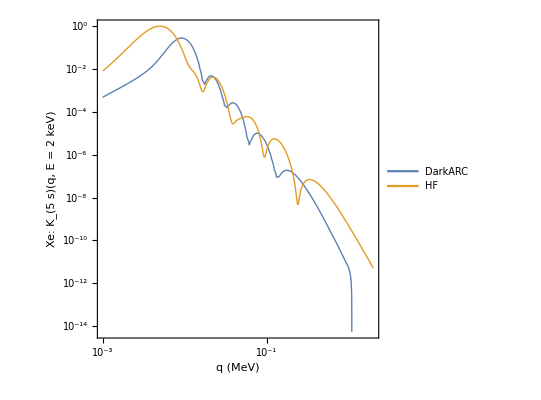
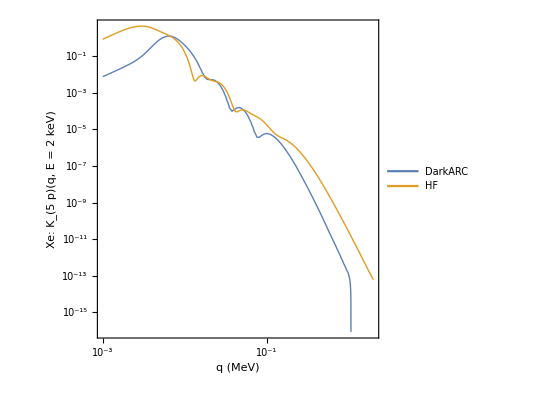

```mathematica
{LogLogPlot[{xe5sFF[q MeV,2keV],intF[[15]][q MeV]},{q,.001,2},
FrameLabel->{"q (MeV)","Xe: K_(5  s)(q, E = 2 keV)"},PlotLegends->Legend[{"DarkARC","HF"}]],
LogLogPlot[{xe5pFF[q MeV,2keV],intF[[16]][q MeV]+intF[[17]][q MeV]},{q,.001,2},
FrameLabel->{"q (MeV)","Xe: K_(5  p)(q, E = 2 keV)"},PlotLegends->Legend[{"DarkARC","HF"}]]}
```

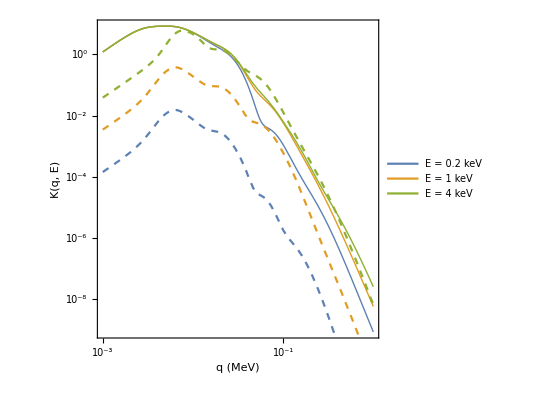

```mathematica
Show[LogLogPlot[{KeStepFull[.2keV,q MeV],KeStepFull[1 keV,q MeV],KeStepFull[4 keV,q MeV]},{q,.001,1},
FrameLabel->{"q (MeV)","K(q, E)"},PlotLegends->Legend[{"E = 0.2 keV","E = 1 keV","E = 4 keV"}]],LogLogPlot[{KeFullStep[.2keV,q MeV],KeFullStep[1keV,q MeV],KeFullStep[4keV,q MeV]},{q,.001,1},PlotStyle->Dashed]]
```

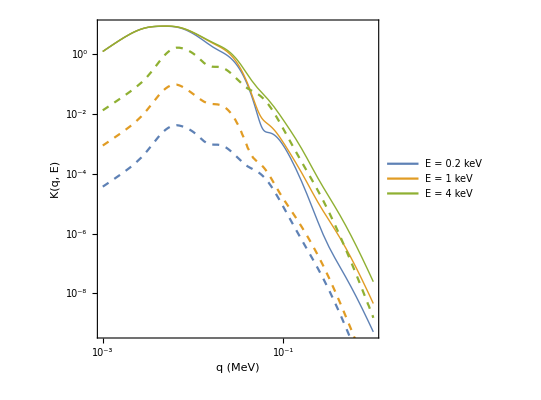

```mathematica
Show[LogLogPlot[{KeStepFull[.1keV,q MeV],KeStepFull[.5 keV,q MeV],KeStepFull[2 keV,q MeV]},{q,.001,1},
FrameLabel->{"q (MeV)","K(q, E)"},PlotLegends->Legend[{"E = 0.2 keV","E = 1 keV","E = 4 keV"}]],LogLogPlot[{KeFull[.1keV,q MeV],KeFullStep[.5keV,q MeV],KeFullStep[2keV,q MeV]},{q,.001,1},PlotStyle->Dashed]]
```

#### Comparing approximations to the DM spectrum

Compare the full rate to the approximation without the form factor:

```mathematica
rateTot5=ParallelTable[{Ex/keV,
10^69 Sum[nN⟦ii⟧dRdEx[Ex,5keV,10^-42 Centimeter^2,5GeV,AN⟦ii⟧],{ii,1,Length[AN]}]},{Ex,0,10keV,.05keV}];
```

```mathematica
rateTot5Approx=ParallelTable[{Ex/keV,
10^69 Sum[nN⟦ii⟧dRdExApprox[Ex,5keV,10^-42 Centimeter^2,5GeV,AN⟦ii⟧],{ii,1,Length[AN]}]},{Ex,0,10keV,.05keV}];
```

```mathematica
rateTot20Heavy=ParallelTable[{Ex/keV,
10^69 Sum[nN⟦ii⟧dRdEx[Ex,5keV,10^-42 Centimeter^2,20GeV,AN⟦ii⟧],{ii,1,Length[AN]}]},{Ex,0,50keV,.05keV}];
```

```mathematica
rateTot20ApproxHeavy=ParallelTable[{Ex/keV,
10^69 Sum[nN⟦ii⟧dRdExApprox[Ex,5keV,10^-42 Centimeter^2,20GeV,AN⟦ii⟧],{ii,1,Length[AN]}]},{Ex,0,50keV,.05keV}];
```

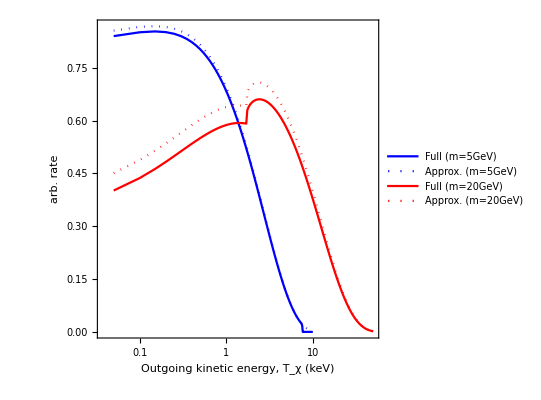

```mathematica
ListLogLinearPlot[{rateTot5,rateTot5Approx,rateTot20Heavy,rateTot20ApproxHeavy},Joined->True,
PlotStyle->{Blue,{Blue,Dotted},Red,{Red,Dotted}},
PlotLegends->Legend[{"Full (m=5GeV)","Approx. (m=5GeV)","Full (m=20GeV)","Approx. (m=20GeV)"},Position->{.25,.2}],
FrameLabel->{"Outgoing kinetic energy, T_χ (keV)","arb. rate"}]
```

Compare the full rate to the rate assuming an average crust target:

```mathematica
rateTot5Avg=ParallelTable[{Ex/keV,10^69 avgN dRdEx[Ex,5keV,10^-42 Centimeter^2,5GeV,avgA]},{Ex,0,8keV,.05keV}];
```

```mathematica
rateTot20Avg=ParallelTable[{Ex/keV,10^69 avgN dRdEx[Ex,5keV,10^-42 Centimeter^2,20GeV,avgA]},{Ex,0,10keV,.05keV}];
```

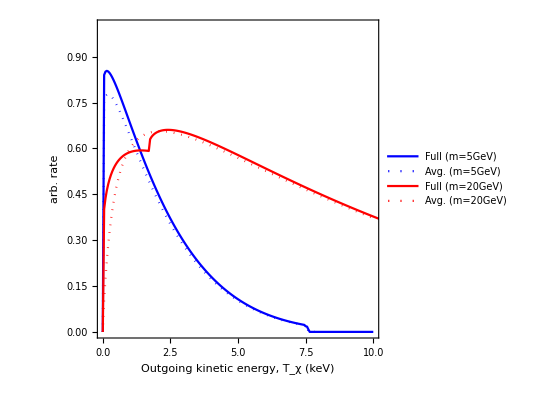

```mathematica
ListPlot[{rateTot5,rateTot5Avg,rateTot20Heavy,rateTot20Avg},Joined->True,
PlotStyle->{Blue,{Blue,Dotted},Red,{Red,Dotted}},PlotRange->{{0,10},{0,1}},
PlotLegends->Legend[{"Full (m=5GeV)","Avg. (m=5GeV)","Full (m=20GeV)","Avg. (m=20GeV)"}],
FrameLabel->{"Outgoing kinetic energy, T_χ (keV)","arb. rate"}]
```

#### Comparing photon spectra

A further approximation can be taken by assuming m_χ<< m_T:

Earth composition from: https://www.sciencedirect.com/science/article/pii/B9780080959757002151

```mathematica
ρE=2.7g/Centimeter^3;
ρM=4.45g/Centimeter^3;
ρC=10.9g/Centimeter^3;
ANs={16,28,27,56,40,39,23,24,58,32};
nNcrust=ρE NA{(.466)/(16 g/mol),(.277)/(28 g/mol),(.081)/(27 g/mol),(.05)/(55.85 g/mol),(.036)/(40 g/mol),(.028)/(39.1 g/mol),(.026)/(23 g/mol),(.021)/(24.3 g/mol),0/(58.7 g/mol),0/(32 g/mol)};(*nuclei/volume*)
nNmantle=ρM NA{(.44)/(16 g/mol),(.21)/(28 g/mol),(.0235)/(27 g/mol),(.0626)/(55.85 g/mol),(.0253)/(40 g/mol),0/(39.1 g/mol),(.0027)/(23 g/mol),(.223)/(24.3 g/mol),0/(58.7 g/mol),0/(32 g/mol)};
nNcore=ρC NA{0/(16 g/mol),(.06)/(28 g/mol),(.0)/(27 g/mol),(.858)/(55.85 g/mol),0/(40 g/mol),0/(39.1 g/mol),0/(23 g/mol),0/(24.3 g/mol),(.052)/(58.7 g/mol),(.019)/(32 g/mol)};
```

```mathematica
dNγdEgApproxAlt[Eg_,δ_,σxp_,mx_,nNs_,V0_:v0,VESC_:vesc]:=
1/EγCoM[mx,δ] Sum[If[nNs[[ii]]>0,
NIntegrate[nNs⟦ii⟧dRdExApprox[Tx,δ,σxp,mx,ANs⟦ii⟧,V0,VESC] (mx+δ)/(2 √((Tx+mx+δ)^2-(mx+δ)^2)),{Tx,TxMin[Eg,mx,δ],TxiMaxGlobal[mx,δ,VESC+Ve[V0]]},PrecisionGoal->3,AccuracyGoal->∞]
,0]
,{ii,Length[ANs]}];
```

Compare the photon spectrum calculated with the approximate DM spectra to the full calculation:

```mathematica
With[{δkeV=5},
dataγfull5=ParallelTable[{Egg/keV,dNγdEG[Egg,δkeV keV,1,5GeV]},{Egg,(δkeV-5 10^-3)keV,(δkeV+5 10^-3)keV,(.1 10^-3)keV}];
dataγfull15=ParallelTable[{Egg/keV,dNγdEG[Egg,δkeV keV,1,15GeV]},{Egg,(δkeV-5 10^-3)keV,(δkeV+5 10^-3)keV,(.1 10^-3)keV}];]
dataγfull5[[All,2]]/=dataγfull5[[51,2]];
dataγfull15[[All,2]]/=dataγfull15[[51,2]];
```

```mathematica
With[{δkeV=5},
dataγApprox5crust=ParallelTable[{Egg/keV,dNγdEgApproxAlt[Egg,δkeV keV,1,5GeV,nNcrust]},{Egg,(δkeV-6 10^-3)keV,(δkeV+6 10^-3)keV,(.1 10^-3)keV}];
dataγApprox15crust=ParallelTable[{Egg/keV,dNγdEgApproxAlt[Egg,δkeV keV,1,15GeV,nNcrust]},{Egg,(δkeV-6 10^-3)keV,(δkeV+6 10^-3)keV,(.1 10^-3)keV}];
dataγApprox5mantle=ParallelTable[{Egg/keV,dNγdEgApproxAlt[Egg,δkeV keV,1,5GeV,nNmantle]},{Egg,(δkeV-6 10^-3)keV,(δkeV+6 10^-3)keV,(.1 10^-3)keV}];
dataγApprox15mantle=ParallelTable[{Egg/keV,dNγdEgApproxAlt[Egg,δkeV keV,1,15GeV,nNmantle]},{Egg,(δkeV-6 10^-3)keV,(δkeV+6 10^-3)keV,(.1 10^-3)keV}];
dataγApprox5core=ParallelTable[{Egg/keV,dNγdEgApproxAlt[Egg,δkeV keV,1,5GeV,nNcore]},{Egg,(δkeV-6 10^-3)keV,(δkeV+6 10^-3)keV,(.1 10^-3)keV}];
dataγApprox15core=ParallelTable[{Egg/keV,dNγdEgApproxAlt[Egg,δkeV keV,1,15GeV,nNcore]},{Egg,(δkeV-6 10^-3)keV,(δkeV+6 10^-3)keV,(.1 10^-3)keV}];]
dataγApprox5crust[[All,2]]/=dataγApprox5crust[[61,2]];
dataγApprox15crust[[All,2]]/=dataγApprox15crust[[61,2]];
dataγApprox5mantle[[All,2]]/=dataγApprox5mantle[[61,2]];
dataγApprox15mantle[[All,2]]/=dataγApprox15mantle[[61,2]];
dataγApprox5core[[All,2]]/=dataγApprox5core[[61,2]];
dataγApprox15core[[All,2]]/=dataγApprox15core[[61,2]];
```

Compare full rate with approximate one:

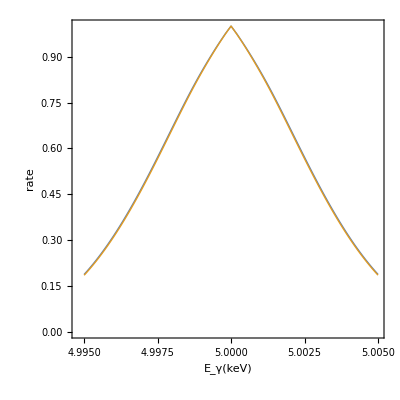

```mathematica
ListPlot[{dataγfull15,dataγApprox15crust},Joined->True,PlotRange->All,FrameLabel->{"E_γ(keV)","rate"}]
```

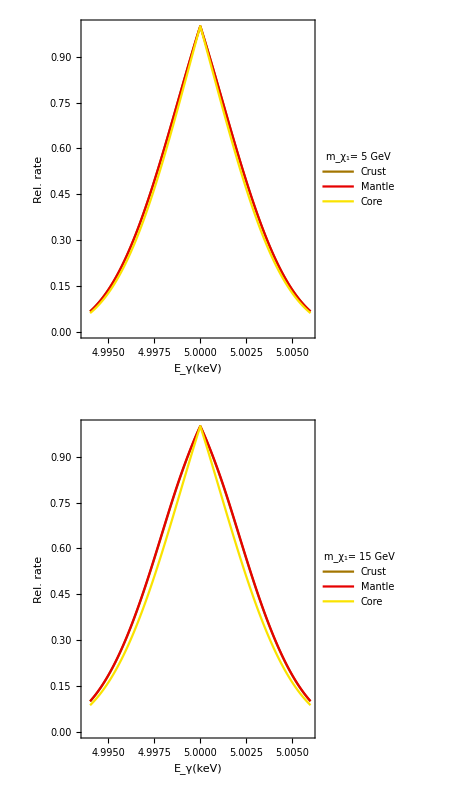

```mathematica
{plot5,plot15}={ListPlot[{dataγApprox5crust,dataγApprox5mantle,dataγApprox5core},Joined->True,PlotRange->All,PlotStyle->{RGBColor[0.64,0.46,0.],RGBColor[0.9,0.,0.],RGBColor[0.98,0.89,0.],{Black,Dashed}},FrameLabel->{"E_γ(keV)","Rel. rate"},
PlotLegends->Legend[{"Crust","Mantle","Core"},Position->{.82,.82},LegendFunction->framed,LegendLabel->Style["m_χ_1= 5 GeV",Black,14]]],
ListPlot[{dataγApprox15crust,dataγApprox15mantle,dataγApprox15core},Joined->True,PlotRange->All,PlotStyle->{RGBColor[0.64,0.46,0.],RGBColor[0.9,0.,0.],RGBColor[0.98,0.89,0.],{Black,Dashed}},FrameLabel->{"E_γ(keV)","Rel. rate"},
PlotLegends->Legend[{"Crust","Mantle","Core"},Position->{.82,.82},LegendFunction->framed,LegendLabel->Style["m_χ_1= 15 GeV",Black,14]]]};
plotGrid[{{plot5},{plot15}},450,800,ImagePadding->50]
```

#### Long-lifetime limit

```mathematica
Psurv[vout_,L_,τ_,Rd_]:=2Sinh[Rd/(2vout τ)]Exp[-L/(vout τ)]
```

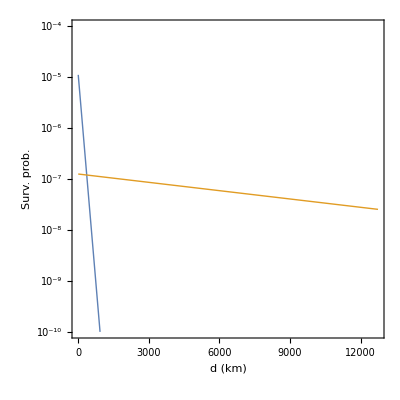

```mathematica
LogPlot[{Psurv[VMAX/10,L 100000Centimeter,1Second,100Centimeter],Psurv[VMAX/10,L 100000Centimeter,100Second,100Centimeter]},{L,10,2 6371},
FrameLabel->{"d (km)","Surv. prob."},
PlotRange->{10^-10,10^-4}]
```

⟶ For lifetimes of ≳100s, there is an approx flat probability of decay for distances < Earth size

Therefore what is the relative contribution of the mantle and core?

Distance to detector from some place in the Earth:

```mathematica
d[R_,r_,θ_]=√(R^2-2r R Cos[θ]+r^2)
```

√(r^2+R^2-2 r R Cos[θ])

Core size as fraction of Earth:

```mathematica
rc=3483/6371//N
```

0.546696

```mathematica
rm=6366/6371//N
```

0.999215

Calculate relative core, mantle and crust contributions:

```mathematica
cC=NIntegrate[(r^2 Sin[θ](ρC/g))/(4π d[1,r,θ]^2),{r,0,rc},{θ,0,π},{ϕ,0,2π}];
mC=NIntegrate[(r^2 Sin[θ](ρM/g))/(4π d[1,r,θ]^2),{r,rc,rm},{θ,0,π},{ϕ,0,2π}];
crC=NIntegrate[(r^2 Sin[θ](ρE/g))/(4π d[1,r,θ]^2),{r,rm,1},{θ,0,π},{ϕ,0,2π}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Fractional contributions:

```mathematica
{crC/(crC+mC+cC),mC/(crC+mC+cC),cC/(crC+mC+cC)}
```

{0.00358848,0.753247,0.243164}

We can ignore the crust in this limit since it is ≲1% of the contribution:

Calculate a weighted average of fluxes that apply in the long-lifetime limit:

```mathematica
dataγApprox5long=dataγApprox5crust;
dataγApprox5long[[All,2]]=crC/(crC+mC+cC)dataγApprox5crust[[All,2]]+mC/(crC+mC+cC) dataγApprox5mantle[[All,2]]+cC/(crC+mC+cC)dataγApprox5core[[All,2]];
dataγApprox15long=dataγApprox15crust;
dataγApprox15long[[All,2]]=crC/(crC+mC+cC)dataγApprox15crust[[All,2]]+mC/(crC+mC+cC) dataγApprox15mantle[[All,2]]+cC/(crC+mC+cC)dataγApprox15core[[All,2]];
```

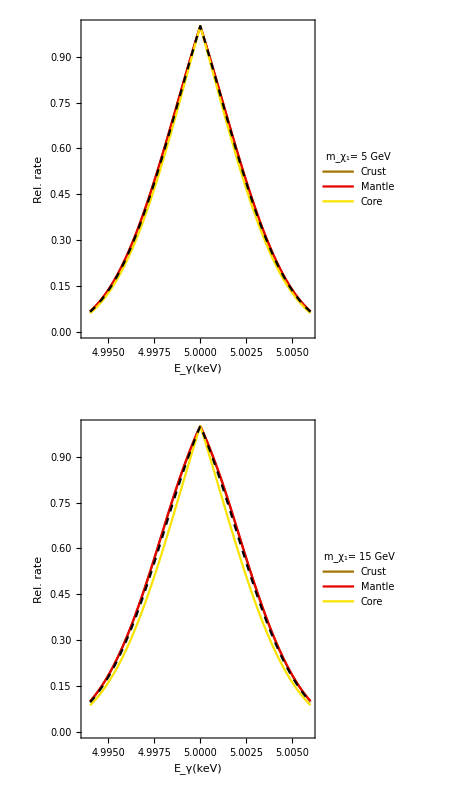

```mathematica
{plot5,plot15}={ListPlot[{dataγApprox5crust,dataγApprox5mantle,dataγApprox5core,dataγApprox5long},Joined->True,PlotRange->All,PlotStyle->{RGBColor[0.64,0.46,0.],RGBColor[0.9,0.,0.],RGBColor[0.98,0.89,0.],{Black,Dashed}},FrameLabel->{"E_γ(keV)","Rel. rate"},
PlotLegends->Legend[{"Crust","Mantle","Core"},Position->{.82,.82},LegendFunction->framed,LegendLabel->Style["m_χ_1= 5 GeV",Black,14]]],
ListPlot[{dataγApprox15crust,dataγApprox15mantle,dataγApprox15core,dataγApprox15long},Joined->True,PlotRange->All,PlotStyle->{RGBColor[0.64,0.46,0.],RGBColor[0.9,0.,0.],RGBColor[0.98,0.89,0.],{Black,Dashed}},FrameLabel->{"E_γ(keV)","Rel. rate"},
PlotLegends->Legend[{"Crust","Mantle","Core"},Position->{.82,.82},LegendFunction->framed,LegendLabel->Style["m_χ_1= 15 GeV",Black,14]]]};
earthPlot=plotGrid[{{plot5},{plot15}},450,800,ImagePadding->50]
```

```mathematica
Export["figures/fig_comb_gamSpecEarth.pdf",earthPlot];
```